# TES - Response (Matrix data)

## Setup

Loads upstream notebooks and points Direc to ../../input/TES.

```mathematica
nbDir = NotebookDirectory[];
Direc = FileNameJoin[{ParentDirectory[ParentDirectory[nbDir]], "input", "TES"}];
Get[FileNameJoin[{nbDir, "07_dcurlyRdEprime_plot.nb"}]];
SetDirectory[Direc];
Print["Direc = ", Direc];
```

## Response function

### Matrix data

#### matrices

```mathematica
(* format *)
```

R(material)M(DM mass)q(heavy/light)Bin(#bin)

```mathematica
(* Repeat these for heavy/light, DM mass, or bin size if needed *)
```

```mathematica
(* Use different kernel for faster calculation *)
```

```mathematica
AbsoluteTiming[RAlM1q0Bin5={
CRvmTES[10 MeV,0][.1,.3],
CRvmTES[10 MeV,0][.3,.5],
CRvmTES[10 MeV,0][.5,.7],
CRvmTES[10 MeV,0][.7,.9],
CRvmTES[10 MeV,0][.9,1.1]}];
```

```mathematica
Export[FileNameJoin[Direc,"Al_R5_q0M1_Ko.h5"],RAlM1q0Bin5]
Export[FileNameJoin[Direc,"Al_R5_q0M1_Ko.csv"],RAlM1q0Bin5]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R5_q0M1_Ko.h5

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R5_q0M1_Ko.csv

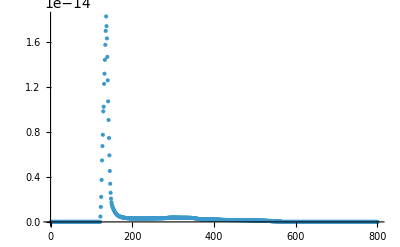

```mathematica
ListPlot[RAlM1q0Bin5[[5]], PlotRange->All]
```

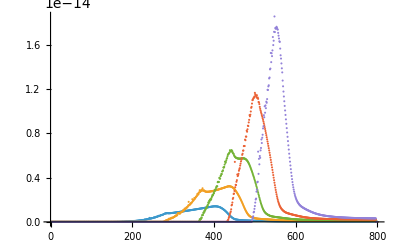

```mathematica
ListPlot[RAlM1q0Bin5, PlotRange->All]
```

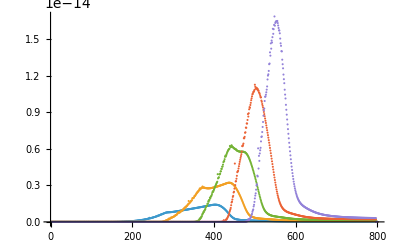

```mathematica
ListPlot[RAlM1q0Bin5, PlotRange->All]
```

```mathematica
Export["/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/CurlyR_TES10MeV_Gaussian.pdf",%293,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/CurlyR_TES10MeV_Gaussian.pdf

```mathematica
AbsoluteTiming[RAlM1q0Bin10={
CRvmTES[10 MeV,0][.1,.2],
CRvmTES[10 MeV,0][.2,.3],
CRvmTES[10 MeV,0][.3,.4],
CRvmTES[10 MeV,0][.4,.5],
CRvmTES[10 MeV,0][.5,.6],
CRvmTES[10 MeV,0][.6,.7],
CRvmTES[10 MeV,0][.7,.8],
CRvmTES[10 MeV,0][.8,.9],
CRvmTES[10 MeV,0][.9,1.0],
CRvmTES[10 MeV,0][1.0,1.1]}]
```

```mathematica
Export[FileNameJoin[Direc,"Al_R10_q0M1.h5"],RAlM1q0Bin10]
Export[FileNameJoin[Direc,"Al_R10_q0M1.csv"],RAlM1q0Bin10]
```

```mathematica
AbsoluteTiming[RAlM2q0Bin5={
CRvmTES[100 MeV,0][.1,.3],
CRvmTES[100 MeV,0][.3,.5],
CRvmTES[100 MeV,0][.5,.7],
CRvmTES[100 MeV,0][.7,.9],
CRvmTES[100 MeV,0][.9,1.1]}]
```

```mathematica
Export[FileNameJoin[Direc,"Al_R5_q0M2_Ko.h5"],RAlM2q0Bin5]
Export[FileNameJoin[Direc,"Al_R5_q0M2_Ko.csv"],RAlM2q0Bin5]
```

```mathematica
AbsoluteTiming[RAlM2q0Bin10={
CRvmTES[100 MeV,0][.1,.2],
CRvmTES[100 MeV,0][.2,.3],
CRvmTES[100 MeV,0][.3,.4],
CRvmTES[100 MeV,0][.4,.5],
CRvmTES[100 MeV,0][.5,.6],
CRvmTES[100 MeV,0][.6,.7],
CRvmTES[100 MeV,0][.7,.8],
CRvmTES[100 MeV,0][.8,.9],
CRvmTES[100 MeV,0][.9,1.0],
CRvmTES[100 MeV,0][1.0,1.1]}]
```

```mathematica
Export[FileNameJoin[Direc,"Al_R10_q0M2.h5"],RAlM2q0Bin10]
Export[FileNameJoin[Direc,"Al_R10_q0M2.csv"],RAlM2q0Bin10]
```

```mathematica
AbsoluteTiming[RAlM3q0Bin5={
CRvmTES[1000 MeV,0][.1,.3],
CRvmTES[1000 MeV,0][.3,.5],
CRvmTES[1000 MeV,0][.5,.7],
CRvmTES[1000 MeV,0][.7,.9],
CRvmTES[1000 MeV,0][.9,1.1]}];
```

```mathematica
Export[FileNameJoin[Direc,"Al_R5_q0M3_Ko_refined_exposure.h5"],RAlM3q0Bin5 * Alexp]
Export[FileNameJoin[Direc,"Al_R5_q0M3_Ko_refined_exposure.csv"],RAlM3q0Bin5 * Alexp]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R5_q0M3_Ko_refined_exposure.h5

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R5_q0M3_Ko_refined_exposure.csv

```mathematica
Export[FileNameJoin[Direc,"Al_R5_q0M3_Ko_refined.h5"],RAlM3q0Bin5]
Export[FileNameJoin[Direc,"Al_R5_q0M3_Ko_refined.csv"],RAlM3q0Bin5]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R5_q0M3_Ko_refined.h5

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R5_q0M3_Ko_refined.csv

```mathematica
AbsoluteTiming[RAlM3q0Bin10={
CRvmTES[1000 MeV,0][.1,.2],
CRvmTES[1000 MeV,0][.2,.3],
CRvmTES[1000 MeV,0][.3,.4],
CRvmTES[1000 MeV,0][.4,.5],
CRvmTES[1000 MeV,0][.5,.6],
CRvmTES[1000 MeV,0][.6,.7],
CRvmTES[1000 MeV,0][.7,.8],
CRvmTES[1000 MeV,0][.8,.9],
CRvmTES[1000 MeV,0][.9,1.0],
CRvmTES[1000 MeV,0][1.0,1.1]}]
```

```mathematica
Export[FileNameJoin[Direc,"Al_R10_q0M3.h5"],RAlM3q0Bin10]
Export[FileNameJoin[Direc,"Al_R10_q0M3.csv"],RAlM3q0Bin10]
```

```mathematica
AbsoluteTiming[RAlM1q0Bin5Left={
CRvmTESLeft[1000 MeV,0][.1,.3],
CRvmTESLeft[1000 MeV,0][.3,.5],
CRvmTESLeft[1000 MeV,0][.5,.7],
CRvmTESLeft[1000 MeV,0][.7,.9],
CRvmTESLeft[1000 MeV,0][.9,1.1]}];
```

```mathematica
AbsoluteTiming[RAlM1q0Bin5Right={
CRvmTESRight[1000 MeV,0][.1,.3],
CRvmTESRight[1000 MeV,0][.3,.5],
CRvmTESRight[1000 MeV,0][.5,.7],
CRvmTESRight[1000 MeV,0][.7,.9],
CRvmTESRight[1000 MeV,0][.9,1.1]}];
```

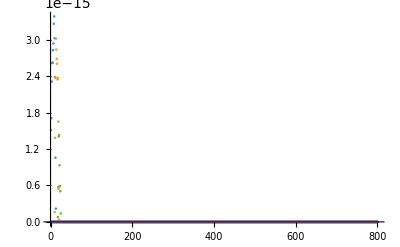

```mathematica
ListPlot[RAlM1q0Bin5Right, PlotRange->All]
```

```mathematica
Export[FileNameJoin[Direc,"Al_R5_q0M3_Right.h5"],RAlM1q0Bin5Right]
Export[FileNameJoin[Direc,"Al_R5_q0M3_Right.csv"],RAlM1q0Bin5Right]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R5_q0M3_Right.h5

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R5_q0M3_Right.csv

```mathematica
AbsoluteTiming[RTiNM1q0Bin5={
CRvmTiN[10 MeV,0][.2,.3],
CRvmTiN[10 MeV,0][.3,.5],
CRvmTiN[10 MeV,0][.5,.7],
CRvmTiN[10 MeV,0][.7,.9],
CRvmTiN[10 MeV,0][.9,1.1]}]
```

{192.471,{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.56068×10^-18,2.07067×10^-17,2.57468×10^-17,4.23864×10^-17,4.59607×10^-17,6.37338×10^-17,1.89113×10^-16,8.53096×10^-17,1.09324×10^-16,1.07838×10^-16,1.27645×10^-16,1.51219×10^-16,1.95745×10^-16,1.69469×10^-16,1.89665×10^-16,2.10707×10^-16,2.32659×10^-16,2.55614×10^-16,2.79503×10^-16,3.03328×10^-16,3.23878×10^-16,3.37891×10^-16,3.47178×10^-16,3.5526×10^-16,3.63405×10^-16,3.71515×10^-16,3.79129×10^-16,3.85684×10^-16,3.90462×10^-16,4.12457×10^-16,4.03814×10^-16,3.95263×10^-16,4.04647×10^-16,3.80504×10^-16,3.61588×10^-16,3.51613×10^-16,3.26669×10^-16,3.11589×10^-16,2.83657×10^-16,2.64091×10^-16,2.36808×10^-16,2.15036×10^-16,2.00924×10^-16,1.68788×10^-16,1.48514×10^-16,1.30913×10^-16,1.1021×10^-16,9.4258×10^-17,8.00804×10^-17,6.77266×10^-17,5.7694×10^-17,4.75496×10^-17,4.00044×10^-17,3.3774×10^-17,2.86815×10^-17,2.45507×10^-17,2.12147×10^-17,1.85234×10^-17,1.6346×10^-17,1.45731×10^-17,1.31204×10^-17,1.19047×10^-17,1.0881×10^-17,1.00061×10^-17,9.24803×10^-18,8.5835×10^-18,7.99432×10^-18,7.46745×10^-18,6.99283×10^-18,6.56262×10^-18,6.17067×10^-18,5.81205×10^-18,5.48274×10^-18,5.1794×10^-18,4.89922×10^-18,4.6398×10^-18,4.39908×10^-18,4.17527×10^-18,3.96679×10^-18,3.77227×10^-18,3.59049×10^-18,3.42036×10^-18,3.26091×10^-18,3.11128×10^-18,2.97069×10^-18,2.83845×10^-18,2.71392×10^-18,2.59652×10^-18,2.48574×10^-18,2.38111×10^-18,2.28219×10^-18,2.18859×10^-18,2.09996×10^-18,2.01595×10^-18},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.4307×10^-20,3.31502×10^-19,4.49877×10^-19,8.63274×10^-19,1.01753×10^-18,1.6635×10^-18,7.007×10^-18,2.85217×10^-18,4.42011×10^-18,4.61152×10^-18,6.46411×10^-18,9.18334×10^-18,1.52239×10^-17,1.26918×10^-17,1.66413×10^-17,2.16534×10^-17,2.79989×10^-17,3.60247×10^-17,4.61146×10^-17,5.83587×10^-17,7.1655×10^-17,8.39408×10^-17,9.50817×10^-17,1.06558×10^-16,1.1928×10^-16,1.3349×10^-16,1.49192×10^-16,1.66321×10^-16,1.84801×10^-16,2.42171×10^-16,2.5327×10^-16,2.71244×10^-16,3.5556×10^-16,3.49435×10^-16,3.6541×10^-16,4.3743×10^-16,4.4191×10^-16,5.25878×10^-16,5.15754×10^-16,5.96018×10^-16,5.81874×10^-16,6.47734×10^-16,9.2279×10^-16,6.89355×10^-16,7.51335×10^-16,9.10607×10^-16,7.61711×10^-16,8.0308×10^-16,8.48813×10^-16,9.11005×10^-16,1.18908×10^-15,8.38102×10^-16,8.54081×10^-16,8.66085×10^-16,8.73639×10^-16,8.76393×10^-16,8.74239×10^-16,8.67342×10^-16,8.56069×10^-16,8.40878×10^-16,9.66745×10^-16,8.93967×10^-16,8.47534×10^-16,8.07498×10^-16,7.69406×10^-16,8.22806×10^-16,7.5418×10^-16,7.02318×10^-16,7.33013×10^-16,6.60068×10^-16,7.09988×10^-16,6.04417×10^-16,6.61857×10^-16,5.36809×10^-16,5.5489×10^-16,4.62808×10^-16,4.53775×10^-16,3.89532×10^-16,3.70422×10^-16,3.55181×10^-16,3.76921×10^-16,2.79713×10^-16,2.59803×10^-16,2.41255×10^-16,2.2495×10^-16,2.14286×10^-16,1.69545×10^-16,1.54024×10^-16,1.39681×10^-16,1.2654×10^-16,1.14611×10^-16,1.03881×10^-16,9.43094×10^-17,9.27609×10^-17},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.19681×10^-23,1.20571×10^-22,1.65082×10^-22,3.37176×10^-22,4.04149×10^-22,6.90871×10^-22,2.83571×10^-21,1.29767×10^-21,2.04317×10^-21,2.25049×10^-21,3.37083×10^-21,5.65359×10^-21,8.48245×10^-21,7.78581×10^-21,1.07039×10^-20,1.49205×10^-20,2.09311×10^-20,2.85333×10^-20,3.94554×10^-20,5.48348×10^-20,7.51005×10^-20,9.54858×10^-20,1.18513×10^-19,1.48681×10^-19,1.8075×10^-19,2.26559×10^-19,2.86002×10^-19,3.48219×10^-19,4.43975×10^-19,6.75597×10^-19,7.86329×10^-19,9.35647×10^-19,1.49608×10^-18,1.6298×10^-18,1.90035×10^-18,2.72878×10^-18,3.09931×10^-18,4.53678×10^-18,4.84202×10^-18,6.80519×10^-18,7.33954×10^-18,9.96804×10^-18,1.88765×10^-17,1.41398×10^-17,1.88399×10^-17,2.81659×10^-17,2.48523×10^-17,3.12421×10^-17,4.01528×10^-17,5.02118×10^-17,8.35246×10^-17,6.03409×10^-17,7.16792×10^-17,8.56853×10^-17,1.00085×10^-16,1.16572×10^-16,1.36168×10^-16,1.53715×10^-16,1.75697×10^-16,2.00626×10^-16,2.65969×10^-16,2.78309×10^-16,3.04158×10^-16,3.2594×10^-16,3.60634×10^-16,4.33094×10^-16,4.67564×10^-16,4.73548×10^-16,5.56739×10^-16,5.72162×10^-16,6.84885×10^-16,6.87383×10^-16,7.99926×10^-16,7.74915×10^-16,8.6853×10^-16,8.75189×10^-16,9.41166×10^-16,9.25015×10^-16,9.8573×10^-16,1.06679×10^-15,1.15965×10^-15,1.03471×10^-15,1.16238×10^-15,1.14452×10^-15,1.18294×10^-15,1.18871×10^-15,1.2926×10^-15,1.15016×10^-15,1.15803×10^-15,1.18381×10^-15,1.16407×10^-15,1.17016×10^-15,1.15022×10^-15,1.16482×10^-15},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.31983×10^-24,2.13612×10^-23,4.78113×10^-23,1.07737×10^-22,1.24212×10^-22,1.9202×10^-22,2.83737×10^-22,5.88945×10^-22,6.26636×10^-22,8.4501×10^-22,1.14002×10^-21,1.42635×10^-21,2.40477×10^-21,2.47875×10^-21,3.51485×10^-21,4.33246×10^-21,5.93532×10^-21,7.09034×10^-21,9.4331×10^-21,1.20131×10^-20,1.52374×10^-20,1.91122×10^-20,2.62334×10^-20,3.16145×10^-20,4.10337×10^-20,5.28172×10^-20,6.27077×10^-20,7.78082×10^-20,1.12078×10^-19,1.30283×10^-19,1.65952×10^-19,2.21513×10^-19,2.44413×10^-19,3.18907×10^-19,4.27524×10^-19,4.65395×10^-19,5.89668×10^-19,7.70641×10^-19,8.88323×10^-19,1.13159×10^-18,1.42261×10^-18,1.66055×10^-18,2.24955×10^-18,2.53628×10^-18,3.02862×10^-18,3.67271×10^-18,5.04882×10^-18,5.51207×10^-18,6.50713×10^-18,7.79911×10^-18,9.49355×10^-18,1.12096×10^-17,1.42187×10^-17,1.69705×10^-17,1.86904×10^-17,2.17664×10^-17,2.57811×10^-17,3.11546×10^-17,3.5681×10^-17,4.74729×10^-17,4.79676×10^-17,5.65862×10^-17,6.60783×10^-17,7.24273×10^-17,8.66234×10^-17,1.01509×10^-16,1.15867×10^-16,1.25705×10^-16,1.39678×10^-16,1.63739×10^-16,1.81283×10^-16,1.98288×10^-16,2.18115×10^-16,2.51703×10^-16,2.7805×10^-16,3.13153×10^-16,3.26435×10^-16,3.72235×10^-16,3.97329×10^-16},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.00539×10^-23,4.73207×10^-23,8.19413×10^-23,1.51626×10^-22,2.32608×10^-22,3.5995×10^-22,5.03528×10^-22,8.10946×10^-22,1.09724×10^-21,1.58219×10^-21,1.80178×10^-21,2.25433×10^-21,3.05575×10^-21,4.03812×10^-21,4.95462×10^-21,6.06961×10^-21,7.54658×10^-21,1.1504×10^-20,1.19986×10^-20,1.61547×10^-20,1.82768×10^-20,2.29246×10^-20,2.83679×10^-20,3.4969×10^-20,4.51565×10^-20,5.29634×10^-20,6.39536×10^-20,7.833×10^-20,9.72791×10^-20,1.1664×10^-19,1.40834×10^-19,1.72625×10^-19,2.02597×10^-19,2.57506×10^-19,3.16874×10^-19,3.74431×10^-19,4.52322×10^-19,5.35338×10^-19,6.43368×10^-19,7.9425×10^-19,9.17949×10^-19,1.09469×10^-18,1.31105×10^-18,1.57967×10^-18,1.89723×10^-18,2.15932×10^-18,2.67645×10^-18,3.23669×10^-18,4.17907×10^-18,4.28332×10^-18,6.03124×10^-18,5.89336×10^-18,7.07837×10^-18,8.07358×10^-18,1.0209×10^-17,1.11606×10^-17,1.32046×10^-17,1.50343×10^-17,1.67926×10^-17,1.9693×10^-17,2.35179×10^-17}}}

```mathematica
Export[FileNameJoin[Direc,"TiN_R5_q0M1_Ko.h5"],RTiNM1q0Bin5]
Export[FileNameJoin[Direc,"TiN_R5_q0M1_Ko.csv"],RTiNM1q0Bin5]
```

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/TiN_R5_q0M1_Ko.h5

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/TiN_R5_q0M1_Ko.csv

```mathematica
AbsoluteTiming[RTiNM1q0Bin10={
CRvmTiN[10 MeV,0][.2,.3],
CRvmTiN[10 MeV,0][.3,.4],
CRvmTiN[10 MeV,0][.4,.5],
CRvmTiN[10 MeV,0][.5,.6],
CRvmTiN[10 MeV,0][.6,.7],
CRvmTiN[10 MeV,0][.7,.8],
CRvmTiN[10 MeV,0][.8,.9],
CRvmTiN[10 MeV,0][.9,1],
CRvmTiN[10 MeV,0][1,1.1]};]
```

```mathematica
Export[FileNameJoin[Direc,"TiN_R10_q0M1.h5"],RTiNM1q0Bin10]
Export[FileNameJoin[Direc,"TiN_R10_q0M1.csv"],RTiNM1q0Bin10]
```

```mathematica
AbsoluteTiming[RTiNM2q0Bin5={
CRvmTiN[100 MeV,0][.2,.3],
CRvmTiN[100 MeV,0][.3,.5],
CRvmTiN[100 MeV,0][.5,.7],
CRvmTiN[100 MeV,0][.7,.9],
CRvmTiN[100 MeV,0][.9,1.1]}]
```

{6874.32,{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.21083×10^-17,4.64929×10^-17,1.53514×10^-16,2.48079×10^-16,3.20687×10^-16,3.71445×10^-16,4.02213×10^-16,4.14345×10^-16,4.09519×10^-16,3.90235×10^-16,3.59993×10^-16,3.22973×10^-16,2.83332×10^-16,2.44513×10^-16,2.08838×10^-16,1.77475×10^-16,1.50693×10^-16,1.282×10^-16,1.09448×10^-16,9.38344×10^-17,8.08024×10^-17,6.98796×10^-17,6.06803×10^-17,5.28946×10^-17,4.6274×10^-17,4.0619×10^-17,3.57685×10^-17,3.15917×10^-17,2.79817×10^-17,2.48508×10^-17,2.21266×10^-17,1.97489×10^-17,1.76674×10^-17,1.58403×10^-17,1.42322×10^-17,1.28133×10^-17,1.15582×10^-17,1.04456×10^-17,9.45702×10^-18,8.57681×10^-18,7.79148×10^-18,7.08944×10^-18,6.46067×10^-18,5.89648×10^-18,5.38937×10^-18,4.93278×10^-18,4.52101×10^-18,4.14907×10^-18,3.81258×10^-18,3.50772×10^-18,3.23112×10^-18,2.9798×10^-18,2.75115×10^-18,2.54284×10^-18,2.35283×10^-18,2.17928×10^-18,2.02059×10^-18,1.87531×10^-18,1.74215×10^-18,1.61997×10^-18,1.50773×10^-18,1.40453×10^-18,1.30952×10^-18,1.22199×10^-18,1.14125×10^-18,1.06671×10^-18,9.97832×10^-19,9.34122×10^-19,8.75142×10^-19,8.20492×10^-19,7.69812×10^-19,7.22773×10^-19,6.79079×10^-19,6.38459×10^-19,6.00667×10^-19,5.65479×10^-19,5.32692×10^-19,5.02119×10^-19,4.73589×10^-19,4.46948×10^-19,4.22053×10^-19,3.98775×10^-19,3.76993×10^-19,3.56598×10^-19,3.37489×10^-19,3.19575×10^-19,3.0277×10^-19,2.86996×10^-19,2.72181×10^-19,2.58258×10^-19,2.45166×10^-19,2.3285×10^-19,2.21256×10^-19,2.10336×10^-19,2.00045×10^-19,1.90343×10^-19,1.8119×10^-19,1.72552×10^-19,1.64395×10^-19,1.56689×10^-19,1.49405×10^-19,1.42517×10^-19,1.36×10^-19,1.29832×10^-19,1.23991×10^-19,1.18458×10^-19,1.13214×10^-19,1.08241×10^-19,1.03524×10^-19,9.90477×10^-20,9.47979×10^-20,9.07618×10^-20,8.69268×10^-20,8.32817×10^-20,7.98157×10^-20,7.65187×10^-20,7.33813×10^-20,7.03946×10^-20,6.75505×10^-20,6.48411×10^-20,6.22591×10^-20,5.97976×10^-20,5.74504×10^-20,5.52112×10^-20,5.30744×10^-20,5.10346×10^-20,4.90868×10^-20,4.72263×10^-20,4.54485×10^-20,4.37493×10^-20,4.21247×10^-20,4.0571×10^-20,3.90845×10^-20,3.7662×10^-20,3.63004×10^-20,3.49965×10^-20,3.37478×10^-20,3.25513×10^-20,3.14047×10^-20,3.03056×10^-20,2.92518×10^-20,2.8241×10^-20,2.72713×10^-20,2.63407×10^-20,2.54475×10^-20,2.45899×10^-20,2.37663×10^-20,2.29752×10^-20,2.22151×10^-20,2.14845×10^-20,2.07823×10^-20,2.0107×10^-20,1.94576×10^-20,1.88329×10^-20,1.82318×10^-20,1.76533×10^-20,1.70964×10^-20,1.65602×10^-20,1.60439×10^-20,1.55465×10^-20,1.50672×10^-20,1.46054×10^-20,1.41603×10^-20,1.37311×10^-20,1.33173×10^-20,1.29182×10^-20,1.25332×10^-20,1.21617×10^-20,1.18033×10^-20,1.14572×10^-20,1.11232×10^-20,1.08006×10^-20,1.04891×10^-20,1.01882×10^-20,9.89742×10^-21,9.61648×10^-21,9.34495×10^-21,9.08248×10^-21,8.8287×10^-21,8.5833×10^-21,8.34596×10^-21,8.11636×10^-21,7.89423×10^-21,7.67928×10^-21,7.47124×10^-21,7.26986×10^-21,7.0749×10^-21,6.88611×10^-21,6.70328×10^-21,6.52618×10^-21,6.35462×10^-21,6.18839×10^-21,6.0273×10^-21,5.87117×10^-21,5.71982×10^-21,5.57309×10^-21,5.4308×10^-21,5.29282×10^-21,5.15898×10^-21,5.02915×10^-21,4.90318×10^-21,4.78095×10^-21,4.66232×10^-21,4.54718×10^-21,4.4354×10^-21,4.32688×10^-21,4.2215×10^-21,4.11915×10^-21,4.01975×10^-21,3.92319×10^-21,3.82937×10^-21,3.73821×10^-21,3.64962×10^-21,3.56352×10^-21,3.47983×10^-21,3.39846×10^-21,3.31935×10^-21,3.24243×10^-21,3.16761×10^-21,3.09484×10^-21,3.02405×10^-21,2.95519×10^-21,2.88818×10^-21,2.82297×10^-21,2.75951×10^-21,2.69774×10^-21,2.63761×10^-21,2.57907×10^-21,2.52208×10^-21,2.46657×10^-21,2.41252×10^-21,2.35987×10^-21,2.30858×10^-21,2.25862×10^-21,2.20994×10^-21,2.16251×10^-21,2.11628×10^-21,2.07123×10^-21,2.02732×10^-21,1.98451×10^-21,1.94277×10^-21,1.90208×10^-21,1.8624×10^-21,1.8237×10^-21,1.78596×10^-21,1.74915×10^-21,1.71323×10^-21,1.6782×10^-21,1.64401×10^-21,1.61065×10^-21,1.5781×10^-21,1.54633×10^-21,1.51532×10^-21,1.48505×10^-21,1.45549×10^-21,1.42664×10^-21,1.39847×10^-21,1.37095×10^-21,1.34409×10^-21,1.31784×10^-21,1.29221×10^-21,1.26717×10^-21,1.24271×10^-21,1.21881×10^-21,1.19545×10^-21,1.17263×10^-21,1.15033×10^-21,1.12853×10^-21,1.10722×10^-21,1.0864×10^-21,1.06603×10^-21,1.04613×10^-21,1.02666×10^-21,1.00763×10^-21,9.89014×10^-22,9.70809×10^-22,9.53004×10^-22,9.35588×10^-22,9.18551×10^-22,9.01883×10^-22,8.85575×10^-22,8.69619×10^-22,8.54005×10^-22,8.38725×10^-22,8.23771×10^-22,8.09135×10^-22,7.94808×10^-22,7.80784×10^-22,7.67055×10^-22,7.53613×10^-22,7.40452×10^-22,7.27566×10^-22,7.14946×10^-22,7.02587×10^-22,6.90484×10^-22,6.78628×10^-22,6.67016×10^-22,6.5564×10^-22,6.44496×10^-22,6.33578×10^-22,6.2288×10^-22,6.12398×10^-22,6.02126×10^-22,5.9206×10^-22,5.82195×10^-22,5.72525×10^-22,5.63047×10^-22,5.53757×10^-22,5.44649×10^-22,5.35721×10^-22,5.26967×10^-22,5.18383×10^-22,5.09967×10^-22,5.01713×10^-22,4.9362×10^-22,4.85682×10^-22,4.77896×10^-22,4.70259×10^-22,4.62769×10^-22,4.5542×10^-22,4.48211×10^-22,4.41139×10^-22,4.34199×10^-22,4.2739×10^-22,4.20709×10^-22,4.14152×10^-22,4.07717×10^-22,4.01402×10^-22,3.95204×10^-22,3.8912×10^-22,3.83148×10^-22,3.77286×10^-22,3.7153×10^-22,3.6588×10^-22,3.60332×10^-22,3.54885×10^-22,3.49537×10^-22,3.44284×10^-22,3.39126×10^-22,3.34061×10^-22,3.29086×10^-22,3.24199×10^-22,3.194×10^-22,3.14685×10^-22,3.10054×10^-22,3.05504×10^-22,3.01033×10^-22,2.96642×10^-22,2.92326×10^-22,2.88086×10^-22,2.8392×10^-22,2.79825×10^-22,2.75801×10^-22,2.71847×10^-22,2.6796×10^-22,2.6414×10^-22,2.60385×10^-22,2.56694×10^-22,2.53065×10^-22,2.49498×10^-22,2.45991×10^-22,2.42543×10^-22,2.39153×10^-22,2.3582×10^-22,2.32542×10^-22,2.29319×10^-22,2.26149×10^-22,2.23032×10^-22,2.19966×10^-22,2.16951×10^-22,2.13985×10^-22,2.11068×10^-22,2.08198×10^-22,2.05375×10^-22,2.02598×10^-22,1.99866×10^-22,1.97178×10^-22,1.94533×10^-22,1.91931×10^-22,1.89371×10^-22,1.86851×10^-22,1.84372×10^-22,1.81932×10^-22,1.79531×10^-22,1.77168×10^-22,1.74842×10^-22,1.72552×10^-22,1.70299×10^-22,1.68081×10^-22,1.65897×10^-22,1.63748×10^-22,1.61631×10^-22,1.59548×10^-22,1.57497×10^-22,1.55477×10^-22,1.53489×10^-22,1.51531×10^-22,1.49603×10^-22,1.47704×10^-22,1.45834×10^-22,1.43993×10^-22,1.4218×10^-22,1.40394×10^-22,1.38634×10^-22,1.36902×10^-22,1.35195×10^-22,1.33514×10^-22,1.31858×10^-22,1.30226×10^-22,1.28619×10^-22,1.27035×10^-22,1.25475×10^-22,1.23938×10^-22,1.22424×10^-22,1.20931×10^-22,1.19461×10^-22,1.18012×10^-22,1.16584×10^-22,1.15177×10^-22,1.1379×10^-22,1.12423×10^-22,1.11076×10^-22,1.09748×10^-22,1.0844×10^-22,1.0715×10^-22,1.05878×10^-22,1.04625×10^-22,1.0339×10^-22,1.02172×10^-22,1.00971×10^-22,9.97868×10^-23,9.86197×10^-23,9.74689×10^-23,9.63342×10^-23,9.52154×10^-23,9.41122×10^-23,9.30243×10^-23,9.19516×10^-23,9.08937×10^-23,8.98504×10^-23,8.88215×10^-23,8.78067×10^-23,8.68059×10^-23,8.58188×10^-23,8.48452×10^-23,8.38848×10^-23,8.29375×10^-23,8.20031×10^-23,8.10813×10^-23,8.01719×10^-23,7.92748×10^-23,7.83898×10^-23,7.75166×10^-23,7.66552×10^-23,7.58052×10^-23,7.49666×10^-23,7.41391×10^-23,7.33225×10^-23,7.25168×10^-23,7.17218×10^-23,7.09372×10^-23,7.01629×10^-23,6.93988×10^-23,6.86447×10^-23,6.79004×10^-23,6.71659×10^-23,6.64408×10^-23,6.57252×10^-23,6.50189×10^-23,6.43217×10^-23,6.36335×10^-23,6.29541×10^-23,6.22835×10^-23,6.16214×10^-23,6.09678×10^-23,6.03225×10^-23,5.96855×10^-23,5.90565×10^-23,5.84356×10^-23,5.78224×10^-23,5.7217×10^-23,5.66192×10^-23,5.6029×10^-23,5.54461×10^-23,5.48705×10^-23,5.43022×10^-23,5.37409×10^-23,5.31865×10^-23,5.26391×10^-23,5.20984×10^-23,5.15644×10^-23,5.1037×10^-23,5.05161×10^-23,5.00016×10^-23,4.94934×10^-23,4.89914×10^-23,4.84955×10^-23,4.80057×10^-23,4.75218×10^-23,4.70438×10^-23,4.65715×10^-23,4.6105×10^-23,4.56441×10^-23,4.51887×10^-23,4.47388×10^-23,4.42943×10^-23,4.38552×10^-23,4.34212×10^-23,4.29924×10^-23,4.25687×10^-23,4.21501×10^-23,4.17364×10^-23,4.13276×10^-23,4.09236×10^-23,4.05243×10^-23,4.01298×10^-23,3.97398×10^-23,3.93544×10^-23,3.89736×10^-23,3.85971×10^-23,3.82251×10^-23,3.78573×10^-23,3.74938×10^-23,3.71346×10^-23,3.67794×10^-23,3.64284×10^-23,3.60813×10^-23,3.57383×10^-23,3.53992×10^-23,3.5064×10^-23,3.47325×10^-23,3.44049×10^-23,3.4081×10^-23,3.37607×10^-23,3.34441×10^-23,3.3131×10^-23,3.28215×10^-23,3.25155×10^-23,3.22129×10^-23,3.19136×10^-23,3.16178×10^-23,3.13252×10^-23,3.10359×10^-23,3.07498×10^-23,3.04669×10^-23,3.01871×10^-23,2.99104×10^-23,2.96368×10^-23,2.93662×10^-23,2.90985×10^-23,2.88338×10^-23,2.8572×10^-23,2.83131×10^-23,2.8057×10^-23,2.78037×10^-23,2.75531×10^-23,2.73052×10^-23,2.70601×10^-23,2.68176×10^-23,2.65777×10^-23,2.63404×10^-23,2.61056×10^-23,2.58734×10^-23,2.56436×10^-23,2.54163×10^-23,2.51915×10^-23,2.4969×10^-23,2.47489×10^-23,2.45311×10^-23,2.43157×10^-23,2.41025×10^-23,2.38916×10^-23,2.36829×10^-23,2.34763×10^-23,2.3272×10^-23,2.30698×10^-23,2.28697×10^-23,2.26717×10^-23,2.24758×10^-23,2.22819×10^-23,2.20901×10^-23,2.19002×10^-23,2.17123×10^-23,2.15263×10^-23,2.13423×10^-23,2.11601×10^-23,2.09798×10^-23,2.08014×10^-23,2.06248×10^-23,2.045×10^-23,2.0277×10^-23,2.01057×10^-23,1.99362×10^-23,1.97685×10^-23,1.96024×10^-23,1.9438×10^-23,1.92752×10^-23,1.91141×10^-23,1.89547×10^-23,1.87968×10^-23,1.86405×10^-23,1.84858×10^-23,1.83326×10^-23,1.8181×10^-23,1.80308×10^-23,1.78822×10^-23,1.7735×10^-23,1.75893×10^-23,1.74451×10^-23,1.73022×10^-23,1.71608×10^-23,1.70208×10^-23,1.68821×10^-23,1.67448×10^-23,1.66089×10^-23,1.64742×10^-23,1.63409×10^-23,1.62089×10^-23,1.60782×10^-23,1.59488×10^-23,1.58206×10^-23,1.56936×10^-23,1.55679×10^-23,1.54434×10^-23,1.53201×10^-23,1.5198×10^-23,1.5077×10^-23,1.49572×10^-23,1.48386×10^-23,1.47211×10^-23,1.46047×10^-23,1.44894×10^-23,1.43752×10^-23,1.42621×10^-23,1.41501×10^-23,1.40391×10^-23,1.39292×10^-23,1.38203×10^-23,1.37125×10^-23,1.36056×10^-23,1.34998×10^-23,1.3395×10^-23,1.32911×10^-23,1.31882×10^-23,1.30863×10^-23,1.29853×10^-23,1.28852×10^-23,1.27861×10^-23,1.26879×10^-23,1.25907×10^-23,1.24943×10^-23,1.23988×10^-23,1.23041×10^-23,1.22104×10^-23,1.21175×10^-23,1.20255×10^-23,1.19343×10^-23,1.18439×10^-23,1.17544×10^-23,1.16657×10^-23,1.15778×10^-23,1.14906×10^-23,1.14043×10^-23,1.13188×10^-23,1.1234×10^-23,1.115×10^-23,1.10668×10^-23,1.09843×10^-23,1.09025×10^-23,1.08215×10^-23,1.07412×10^-23,1.06616×10^-23,1.05827×10^-23,1.05046×10^-23,1.04271×10^-23,1.03503×10^-23,1.02742×10^-23,1.01988×10^-23,1.0124×10^-23,1.00499×10^-23,9.97649×10^-24,9.9037×10^-24,9.83154×10^-24,9.76002×10^-24,9.68912×10^-24,9.61884×10^-24,9.54918×10^-24,9.48013×10^-24,9.41168×10^-24,9.34382×10^-24,9.27656×10^-24,9.20987×10^-24,9.14377×10^-24,9.07824×10^-24,9.01327×10^-24,8.94886×10^-24,8.88501×10^-24,8.82171×10^-24,8.75895×10^-24,8.69673×10^-24,8.63504×10^-24,8.57388×10^-24,8.51324×10^-24,8.45312×10^-24,8.39351×10^-24,8.3344×10^-24,8.2758×10^-24,8.2177×10^-24,8.16008×10^-24,8.10295×10^-24,8.04631×10^-24,7.99014×10^-24,7.93445×10^-24,7.87922×10^-24,7.82445×10^-24,7.77015×10^-24,7.7163×10^-24,7.66289×10^-24,7.60994×10^-24,7.55742×10^-24,7.50534×10^-24,7.4537×10^-24,7.40248×10^-24,7.35169×10^-24,7.30131×10^-24,7.25136×10^-24,7.20181×10^-24,7.15267×10^-24,7.10394×10^-24,7.05561×10^-24,7.00767×10^-24,6.96012×10^-24,6.91297×10^-24,6.8662×10^-24,6.81981×10^-24,6.77379×10^-24,6.72816×10^-24,6.68289×10^-24,6.63799×10^-24,6.59345×10^-24,6.54927×10^-24,6.50545×10^-24,6.46199×10^-24,6.41887×10^-24,6.3761×10^-24,6.33367×10^-24,6.29159×10^-24,6.24984×10^-24,6.20842×10^-24,6.16734×10^-24,6.12658×10^-24,6.08614×10^-24,6.04603×10^-24,6.00624×10^-24,5.96676×10^-24,5.9276×10^-24,5.88874×10^-24,5.8502×10^-24,5.81195×10^-24,5.77401×10^-24,5.73636×10^-24,5.69902×10^-24,5.66196×10^-24,5.62519×10^-24,5.58872×10^-24,5.55252×10^-24,5.51661×10^-24,5.48098×10^-24,5.44563×10^-24,5.41055×10^-24,5.37575×10^-24,5.34121×10^-24,5.30694×10^-24,5.27294×10^-24,5.23919×10^-24,5.20571×10^-24,5.17249×10^-24,5.13952×10^-24,5.1068×10^-24,5.07434×10^-24,5.04212×10^-24},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.95704×10^-19,1.60948×10^-18,6.33238×10^-18,1.58497×10^-17,3.19842×10^-17,5.5399×10^-17,8.88265×10^-17,1.3366×10^-16,1.8936×10^-16,2.53988×10^-16,3.22804×10^-16,3.92574×10^-16,4.59363×10^-16,5.20686×10^-16,5.75091×10^-16,6.21886×10^-16,6.60817×10^-16,6.91805×10^-16,7.14782×10^-16,7.29647×10^-16,7.36313×10^-16,7.34796×10^-16,7.25303×10^-16,7.08299×10^-16,6.84531×10^-16,6.55007×10^-16,6.20932×10^-16,5.83625×10^-16,5.44409×10^-16,5.04522×10^-16,4.65038×10^-16,4.26822×10^-16,3.9051×10^-16,3.56518×10^-16,3.25072×10^-16,2.96242×10^-16,2.69983×10^-16,2.46173×10^-16,2.24646×10^-16,2.05212×10^-16,1.87676×10^-16,1.71849×10^-16,1.57557×10^-16,1.44636×10^-16,1.3294×10^-16,1.22341×10^-16,1.12721×10^-16,1.03979×10^-16,9.60232×10^-17,8.87736×10^-17,8.21588×10^-17,7.61155×10^-17,7.05875×10^-17,6.55249×10^-17,6.08831×10^-17,5.66222×10^-17,5.27068×10^-17,4.9105×10^-17,4.57882×10^-17,4.27309×10^-17,3.991×10^-17,3.73046×10^-17,3.48962×10^-17,3.26678×10^-17,3.06041×10^-17,2.86913×10^-17,2.69169×10^-17,2.52696×10^-17,2.37389×10^-17,2.23156×10^-17,2.09911×10^-17,1.97576×10^-17,1.86081×10^-17,1.75359×10^-17,1.65354×10^-17,1.56009×10^-17,1.47276×10^-17,1.39109×10^-17,1.31466×10^-17,1.2431×10^-17,1.17606×10^-17,1.1132×10^-17,1.05424×10^-17,9.98891×10^-18,9.46913×10^-18,8.98071×10^-18,8.52149×10^-18,8.0895×10^-18,7.6829×10^-18,7.29999×10^-18,6.93923×10^-18,6.59914×10^-18,6.27838×10^-18,5.97572×10^-18,5.68998×10^-18,5.42011×10^-18,5.16508×10^-18,4.92399×10^-18,4.69596×10^-18,4.48019×10^-18,4.27593×10^-18,4.08249×10^-18,3.89921×10^-18,3.72549×10^-18,3.56076×10^-18,3.4045×10^-18,3.2562×10^-18,3.11541×10^-18,2.9817×10^-18,2.85466×10^-18,2.73391×10^-18,2.6191×10^-18,2.50989×10^-18,2.40599×10^-18,2.30708×10^-18,2.21291×10^-18,2.12321×10^-18,2.03774×10^-18,1.95627×10^-18,1.8786×10^-18,1.80451×10^-18,1.73383×10^-18,1.66637×10^-18,1.60196×10^-18,1.54046×10^-18,1.4817×10^-18,1.42556×10^-18,1.37189×10^-18,1.32058×10^-18,1.2715×10^-18,1.22455×10^-18,1.17962×10^-18,1.13662×10^-18,1.09544×10^-18,1.056×10^-18,1.01821×10^-18,9.82003×10^-19,9.47296×10^-19,9.1402×10^-19,8.82108×10^-19,8.51496×10^-19,8.22123×10^-19,7.93933×10^-19,7.6687×10^-19,7.40885×10^-19,7.15927×10^-19,6.91951×10^-19,6.68912×10^-19,6.46769×10^-19,6.25482×10^-19,6.05013×10^-19,5.85326×10^-19,5.66388×10^-19,5.48166×10^-19,5.30628×10^-19,5.13746×10^-19,4.97492×10^-19,4.81839×10^-19,4.66762×10^-19,4.52236×10^-19,4.38238×10^-19,4.24747×10^-19,4.11742×10^-19,3.99202×10^-19,3.87109×10^-19,3.75444×10^-19,3.64191×10^-19,3.53332×10^-19,3.42852×10^-19,3.32736×10^-19,3.22969×10^-19,3.13537×10^-19,3.04428×10^-19,2.95628×10^-19,2.87127×10^-19,2.78911×10^-19,2.70971×10^-19,2.63295×10^-19,2.55874×10^-19,2.48698×10^-19,2.41758×10^-19,2.35044×10^-19,2.28549×10^-19,2.22264×10^-19,2.16182×10^-19,2.10295×10^-19,2.04595×10^-19,1.99077×10^-19,1.93733×10^-19,1.88557×10^-19,1.83543×10^-19,1.78686×10^-19,1.73979×10^-19,1.69418×10^-19,1.64997×10^-19,1.60711×10^-19,1.56556×10^-19,1.52526×10^-19,1.48619×10^-19,1.44828×10^-19,1.41152×10^-19,1.37584×10^-19,1.34123×10^-19,1.30764×10^-19,1.27503×10^-19,1.24338×10^-19,1.21265×10^-19,1.18281×10^-19,1.15384×10^-19,1.12569×10^-19,1.09836×10^-19,1.0718×10^-19,1.046×10^-19,1.02092×10^-19,9.96554×10^-20,9.72869×10^-20,9.49846×10^-20,9.27462×10^-20,9.05699×10^-20,8.84535×10^-20,8.63952×10^-20,8.43932×10^-20,8.24458×10^-20,8.05511×10^-20,7.87076×10^-20,7.69137×10^-20,7.51679×10^-20,7.34687×10^-20,7.18146×10^-20,7.02043×10^-20,6.86365×10^-20,6.71098×10^-20,6.56231×10^-20,6.41751×10^-20,6.27646×10^-20,6.13907×10^-20,6.00521×10^-20,5.87479×10^-20,5.74769×10^-20,5.62384×10^-20,5.50312×10^-20,5.38546×10^-20,5.27075×10^-20,5.15892×10^-20,5.04988×10^-20,4.94355×10^-20,4.83986×10^-20,4.73873×10^-20,4.64009×10^-20,4.54387×10^-20,4.44999×10^-20,4.3584×10^-20,4.26903×10^-20,4.18182×10^-20,4.0967×10^-20,4.01363×10^-20,3.93254×10^-20,3.85338×10^-20,3.7761×10^-20,3.70064×10^-20,3.62696×10^-20,3.55501×10^-20,3.48474×10^-20,3.41611×10^-20,3.34907×10^-20,3.28359×10^-20,3.21961×10^-20,3.1571×10^-20,3.09602×10^-20,3.03633×10^-20,2.978×10^-20,2.921×10^-20,2.86527×10^-20,2.81081×10^-20,2.75756×10^-20,2.7055×10^-20,2.65461×10^-20,2.60484×10^-20,2.55617×10^-20,2.50858×10^-20,2.46203×10^-20,2.4165×10^-20,2.37196×10^-20,2.32839×10^-20,2.28577×10^-20,2.24406×10^-20,2.20326×10^-20,2.16333×10^-20,2.12426×10^-20,2.08601×10^-20,2.04858×10^-20,2.01195×10^-20,1.97609×10^-20,1.94098×10^-20,1.90661×10^-20,1.87295×10^-20,1.84×10^-20,1.80774×10^-20,1.77614×10^-20,1.74519×10^-20,1.71488×10^-20,1.68519×10^-20,1.65611×10^-20,1.62763×10^-20,1.59972×10^-20,1.57238×10^-20,1.54559×10^-20,1.51934×10^-20,1.49361×10^-20,1.4684×10^-20,1.44369×10^-20,1.41948×10^-20,1.39574×10^-20,1.37248×10^-20,1.34967×10^-20,1.32731×10^-20,1.30539×10^-20,1.2839×10^-20,1.26282×10^-20,1.24216×10^-20,1.22189×10^-20,1.20202×10^-20,1.18252×10^-20,1.16341×10^-20,1.14465×10^-20,1.12626×10^-20,1.10821×10^-20,1.09051×10^-20,1.07314×10^-20,1.0561×10^-20,1.03938×10^-20,1.02297×10^-20,1.00687×10^-20,9.91068×10^-21,9.7556×10^-21,9.60339×10^-21,9.454×10^-21,9.30735×10^-21,9.1634×10^-21,9.02208×10^-21,8.88335×10^-21,8.74714×10^-21,8.61341×10^-21,8.48209×10^-21,8.35315×10^-21,8.22653×10^-21,8.10218×10^-21,7.98006×10^-21,7.86011×10^-21,7.74231×10^-21,7.62659×10^-21,7.51293×10^-21,7.40127×10^-21,7.29158×10^-21,7.18381×10^-21,7.07793×10^-21,6.9739×10^-21,6.87169×10^-21,6.77125×10^-21,6.67255×10^-21,6.57555×10^-21,6.48023×10^-21,6.38654×10^-21,6.29446×10^-21,6.20395×10^-21,6.11499×10^-21,6.02754×10^-21,5.94157×10^-21,5.85706×10^-21,5.77397×10^-21,5.69228×10^-21,5.61196×10^-21,5.53299×10^-21,5.45533×10^-21,5.37897×10^-21,5.30387×10^-21,5.23002×10^-21,5.15739×10^-21,5.08595×10^-21,5.01569×10^-21,4.94658×10^-21,4.87861×10^-21,4.81174×10^-21,4.74595×10^-21,4.68124×10^-21,4.61757×10^-21,4.55493×10^-21,4.4933×10^-21,4.43266×10^-21,4.37299×10^-21,4.31428×10^-21,4.2565×10^-21,4.19964×10^-21,4.14368×10^-21,4.0886×10^-21,4.0344×10^-21,3.98105×10^-21,3.92854×10^-21,3.87685×10^-21,3.82597×10^-21,3.77588×10^-21,3.72657×10^-21,3.67803×10^-21,3.63023×10^-21,3.58318×10^-21,3.53685×10^-21,3.49123×10^-21,3.44631×10^-21,3.40208×10^-21,3.35852×10^-21,3.31563×10^-21,3.27338×10^-21,3.23178×10^-21,3.1908×10^-21,3.15045×10^-21,3.1107×10^-21,3.07154×10^-21,3.03297×10^-21,2.99498×10^-21,2.95755×10^-21,2.92068×10^-21,2.88436×10^-21,2.84857×10^-21,2.81332×10^-21,2.77858×10^-21,2.74435×10^-21,2.71062×10^-21,2.67739×10^-21,2.64464×10^-21,2.61236×10^-21,2.58056×10^-21,2.54922×10^-21,2.51833×10^-21,2.48788×10^-21,2.45787×10^-21,2.4283×10^-21,2.39915×10^-21,2.37041×10^-21,2.34208×10^-21,2.31416×10^-21,2.28663×10^-21,2.2595×10^-21,2.23274×10^-21,2.20637×10^-21,2.18036×10^-21,2.15472×10^-21,2.12944×10^-21,2.10451×10^-21,2.07993×10^-21,2.05569×10^-21,2.03179×10^-21,2.00822×10^-21,1.98497×10^-21,1.96205×10^-21,1.93944×10^-21,1.91714×10^-21,1.89515×10^-21,1.87345×10^-21,1.85206×10^-21,1.83095×10^-21,1.81013×10^-21,1.78959×10^-21,1.76933×10^-21,1.74935×10^-21,1.72963×10^-21,1.71018×10^-21,1.69099×10^-21,1.67205×10^-21,1.65337×10^-21,1.63494×10^-21,1.61675×10^-21,1.5988×10^-21,1.5811×10^-21,1.56362×10^-21,1.54638×10^-21,1.52936×10^-21,1.51256×10^-21,1.49599×10^-21,1.47963×10^-21,1.46349×10^-21,1.44755×10^-21,1.43182×10^-21,1.4163×10^-21,1.40098×10^-21,1.38585×10^-21,1.37092×10^-21,1.35618×10^-21,1.34164×10^-21,1.32727×10^-21,1.31309×10^-21,1.29909×10^-21,1.28527×10^-21,1.27163×10^-21,1.25816×10^-21,1.24486×10^-21,1.23172×10^-21,1.21875×10^-21,1.20595×10^-21,1.1933×10^-21,1.18082×10^-21,1.16849×10^-21,1.15631×10^-21,1.14429×10^-21,1.13241×10^-21,1.12068×10^-21,1.1091×10^-21,1.09766×10^-21,1.08636×10^-21,1.0752×10^-21,1.06417×10^-21,1.05329×10^-21,1.04253×10^-21,1.03191×10^-21,1.02141×10^-21,1.01105×10^-21,1.0008×10^-21,9.90686×10^-22,9.80691×10^-22,9.70817×10^-22,9.61061×10^-22,9.51422×10^-22,9.41899×10^-22,9.3249×10^-22,9.23193×10^-22,9.14007×10^-22,9.04931×10^-22,8.95962×10^-22,8.87099×10^-22,8.78341×10^-22,8.69687×10^-22,8.61135×10^-22,8.52683×10^-22,8.4433×10^-22,8.36076×10^-22,8.27917×10^-22,8.19854×10^-22,8.11885×10^-22,8.04009×10^-22,7.96224×10^-22,7.88529×10^-22,7.80924×10^-22,7.73406×10^-22,7.65974×10^-22,7.58628×10^-22,7.51367×10^-22,7.44188×10^-22,7.37092×10^-22,7.30076×10^-22,7.23141×10^-22,7.16284×10^-22,7.09506×10^-22,7.02804×10^-22,6.96177×10^-22,6.89626×10^-22,6.83149×10^-22,6.76744×10^-22,6.70411×10^-22,6.64149×10^-22,6.57957×10^-22,6.51835×10^-22,6.4578×10^-22,6.39793×10^-22,6.33872×10^-22,6.28017×10^-22,6.22227×10^-22,6.16501×10^-22,6.10838×10^-22,6.05237×10^-22,5.99698×10^-22,5.94219×10^-22,5.88801×10^-22,5.83441×10^-22,5.78141×10^-22,5.72897×10^-22,5.67711×10^-22,5.62581×10^-22,5.57507×10^-22,5.52487×10^-22,5.47522×10^-22,5.4261×10^-22,5.37751×10^-22,5.32944×10^-22,5.28189×10^-22,5.23484×10^-22,5.1883×10^-22,5.14225×10^-22,5.0967×10^-22,5.05163×10^-22,5.00703×10^-22,4.96291×10^-22,4.91925×10^-22,4.87606×10^-22,4.83332×10^-22,4.79103×10^-22,4.74918×10^-22,4.70777×10^-22,4.6668×10^-22,4.62625×10^-22,4.58612×10^-22,4.54641×10^-22,4.50712×10^-22,4.46823×10^-22,4.42975×10^-22,4.39166×10^-22,4.35397×10^-22,4.31666×10^-22,4.27974×10^-22,4.24319×10^-22,4.20703×10^-22,4.17123×10^-22,4.13579×10^-22,4.10072×10^-22,4.06601×10^-22,4.03165×10^-22,3.99763×10^-22,3.96396×10^-22,3.93063×10^-22,3.89764×10^-22,3.86498×10^-22,3.83265×10^-22,3.80065×10^-22,3.76896×10^-22,3.73759×10^-22,3.70654×10^-22,3.6758×10^-22,3.64536×10^-22,3.61522×10^-22,3.58539×10^-22,3.55585×10^-22,3.5266×10^-22,3.49764×10^-22,3.46897×10^-22,3.44058×10^-22,3.41246×10^-22,3.38463×10^-22,3.35707×10^-22,3.32977×10^-22,3.30275×10^-22,3.27598×10^-22,3.24948×10^-22,3.22324×10^-22,3.19725×10^-22,3.17151×10^-22,3.14602×10^-22,3.12078×10^-22,3.09578×10^-22,3.07102×10^-22,3.0465×10^-22,3.02222×10^-22,2.99816×10^-22,2.97434×10^-22,2.95075×10^-22,2.92738×10^-22,2.90423×10^-22,2.88131×10^-22,2.8586×10^-22,2.8361×10^-22,2.81382×10^-22,2.79175×10^-22,2.76989×10^-22,2.74823×10^-22,2.72678×10^-22,2.70553×10^-22,2.68448×10^-22,2.66362×10^-22,2.64296×10^-22,2.62249×10^-22,2.60222×10^-22,2.58213×10^-22,2.56223×10^-22,2.54251×10^-22,2.52298×10^-22,2.50363×10^-22,2.48445×10^-22,2.46545×10^-22,2.44663×10^-22,2.42798×10^-22,2.4095×10^-22,2.39119×10^-22,2.37305×10^-22,2.35507×10^-22,2.33726×10^-22,2.31961×10^-22,2.30212×10^-22,2.28479×10^-22,2.26761×10^-22,2.25059×10^-22,2.23373×10^-22,2.21701×10^-22,2.20045×10^-22,2.18404×10^-22,2.16777×10^-22,2.15165×10^-22,2.13568×10^-22,2.11984×10^-22,2.10415×10^-22,2.0886×10^-22,2.07319×10^-22,2.05791×10^-22,2.04277×10^-22,2.02776×10^-22,2.01289×10^-22,1.99815×10^-22,1.98354×10^-22,1.96905×10^-22,1.9547×10^-22,1.94047×10^-22,1.92636×10^-22,1.91238×10^-22,1.89852×10^-22,1.88478×10^-22,1.87116×10^-22,1.85766×10^-22,1.84428×10^-22,1.83102×10^-22,1.81786×10^-22,1.80483×10^-22,1.7919×10^-22,1.77909×10^-22,1.76639×10^-22,1.75379×10^-22,1.74131×10^-22,1.72893×10^-22,1.71666×10^-22,1.70449×10^-22,1.69243×10^-22,1.68047×10^-22,1.66861×10^-22,1.65685×10^-22,1.64519×10^-22,1.63363×10^-22,1.62217×10^-22,1.61081×10^-22,1.59954×10^-22,1.58837×10^-22,1.57729×10^-22,1.56631×10^-22,1.55541×10^-22,1.54461×10^-22,1.5339×10^-22,1.52328×10^-22,1.51274×10^-22,1.5023×10^-22,1.49194×10^-22,1.48167×10^-22,1.47148×10^-22,1.46138×10^-22,1.45136×10^-22,1.44143×10^-22,1.43157×10^-22,1.4218×10^-22,1.41211×10^-22,1.4025×10^-22,1.39296×10^-22,1.38351×10^-22,1.37413×10^-22,1.36483×10^-22,1.3556×10^-22,1.34645×10^-22,1.33738×10^-22,1.32838×10^-22,1.31945×10^-22,1.31059×10^-22,1.30181×10^-22,1.29309×10^-22,1.28445×10^-22,1.27588×10^-22,1.26738×10^-22,1.25894×10^-22,1.25057×10^-22,1.24227×10^-22,1.23404×10^-22,1.22587×10^-22,1.21777×10^-22,1.20973×10^-22,1.20175×10^-22,1.19384×10^-22,1.18599×10^-22,1.17821×10^-22,1.17048×10^-22,1.16282×10^-22},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.21809×10^-22,7.83124×10^-22,3.80623×10^-21,1.4036×10^-20,4.62033×10^-20,1.28454×10^-19,3.28197×10^-19,7.81283×10^-19,1.69468×10^-18,3.50377×10^-18,6.14019×10^-18,1.00688×10^-17,1.52248×10^-17,2.18428×10^-17,3.01284×10^-17,4.07132×10^-17,5.44293×10^-17,7.19297×10^-17,9.41828×10^-17,1.21854×10^-16,1.55459×10^-16,1.95058×10^-16,2.40517×10^-16,2.91164×10^-16,3.45996×10^-16,4.03699×10^-16,4.62752×10^-16,5.21539×10^-16,5.78469×10^-16,6.32072×10^-16,6.81077×10^-16,7.24449×10^-16,7.61414×10^-16,7.91447×10^-16,8.14263×10^-16,8.29787×10^-16,8.38134×10^-16,8.39585×10^-16,8.34563×10^-16,8.2361×10^-16,8.07362×10^-16,7.86526×10^-16,7.61849×10^-16,7.34093×10^-16,7.04007×10^-16,6.72304×10^-16,6.39642×10^-16,6.06607×10^-16,5.73702×10^-16,5.41347×10^-16,5.09877×10^-16,4.79544×10^-16,4.5053×10^-16,4.22951×10^-16,3.96871×10^-16,3.7231×10^-16,3.49255×10^-16,3.27666×10^-16,3.07488×10^-16,2.88652×10^-16,2.71084×10^-16,2.54707×10^-16,2.39443×10^-16,2.25215×10^-16,2.11951×10^-16,1.99581×10^-16,1.8804×10^-16,1.77266×10^-16,1.67205×10^-16,1.57802×10^-16,1.49009×10^-16,1.40783×10^-16,1.33081×10^-16,1.25867×10^-16,1.19104×10^-16,1.12762×10^-16,1.0681×10^-16,1.01222×10^-16,9.59712×10^-17,9.10355×10^-17,8.63933×10^-17,8.20247×10^-17,7.79115×10^-17,7.40367×10^-17,7.03847×10^-17,6.69409×10^-17,6.36918×10^-17,6.0625×10^-17,5.77289×10^-17,5.49927×10^-17,5.24064×10^-17,4.99606×10^-17,4.76468×10^-17,4.54569×10^-17,4.33833×10^-17,4.1419×10^-17,3.95575×10^-17,3.77928×10^-17,3.6119×10^-17,3.4531×10^-17,3.30237×10^-17,3.15924×10^-17,3.02329×10^-17,2.8941×10^-17,2.7713×10^-17,2.65452×10^-17,2.54343×10^-17,2.43772×10^-17,2.33709×10^-17,2.24127×10^-17,2.14999×10^-17,2.06302×10^-17,1.98011×10^-17,1.90106×10^-17,1.82567×10^-17,1.75373×10^-17,1.68507×10^-17,1.61953×10^-17,1.55694×10^-17,1.49714×10^-17,1.44001×10^-17,1.3854×10^-17,1.33319×10^-17,1.28326×10^-17,1.2355×10^-17,1.18979×10^-17,1.14604×10^-17,1.10416×10^-17,1.06405×10^-17,1.02563×10^-17,9.88816×10^-18,9.53534×10^-18,9.19712×10^-18,8.8728×10^-18,8.56174×10^-18,8.26333×10^-18,7.97698×10^-18,7.70214×10^-18,7.43828×10^-18,7.18491×10^-18,6.94154×10^-18,6.70775×10^-18,6.48309×10^-18,6.26716×10^-18,6.05957×10^-18,5.85997×10^-18,5.668×10^-18,5.48333×10^-18,5.30564×10^-18,5.13464×10^-18,4.97004×10^-18,4.81157×10^-18,4.65897×10^-18,4.51198×10^-18,4.37039×10^-18,4.23396×10^-18,4.10247×10^-18,3.97573×10^-18,3.85354×10^-18,3.73571×10^-18,3.62207×10^-18,3.51245×10^-18,3.40669×10^-18,3.30463×10^-18,3.20612×10^-18,3.11103×10^-18,3.01921×10^-18,2.93055×10^-18,2.84492×10^-18,2.7622×10^-18,2.68227×10^-18,2.60504×10^-18,2.53039×10^-18,2.45823×10^-18,2.38847×10^-18,2.32101×10^-18,2.25577×10^-18,2.19266×10^-18,2.13161×10^-18,2.07254×10^-18,2.01537×10^-18,1.96004×10^-18,1.90648×10^-18,1.85462×10^-18,1.8044×10^-18,1.75577×10^-18,1.70867×10^-18,1.66304×10^-18,1.61882×10^-18,1.57598×10^-18,1.53446×10^-18,1.49421×10^-18,1.45519×10^-18,1.41736×10^-18,1.38068×10^-18,1.3451×10^-18,1.3106×10^-18,1.27712×10^-18,1.24464×10^-18,1.21313×10^-18,1.18254×10^-18,1.15285×10^-18,1.12404×10^-18,1.09606×10^-18,1.0689×10^-18,1.04252×10^-18,1.0169×10^-18,9.92012×10^-19,9.67837×10^-19,9.44349×10^-19,9.21527×10^-19,8.99349×10^-19,8.77793×10^-19,8.5684×10^-19,8.36472×10^-19,8.16668×10^-19,7.97412×10^-19,7.78685×10^-19,7.60473×10^-19,7.42757×10^-19,7.25524×10^-19,7.08757×10^-19,6.92443×10^-19,6.76568×10^-19,6.61118×10^-19,6.4608×10^-19,6.31441×10^-19,6.1719×10^-19,6.03315×10^-19,5.89804×10^-19,5.76646×10^-19,5.63832×10^-19,5.51351×10^-19,5.39192×10^-19,5.27347×10^-19,5.15806×10^-19,5.0456×10^-19,4.93601×10^-19,4.8292×10^-19,4.72509×10^-19,4.62361×10^-19,4.52467×10^-19,4.42821×10^-19,4.33416×10^-19,4.24244×10^-19,4.15299×10^-19,4.06575×10^-19,3.98065×10^-19,3.89764×10^-19,3.81665×10^-19,3.73763×10^-19,3.66052×10^-19,3.58527×10^-19,3.51184×10^-19,3.44016×10^-19,3.3702×10^-19,3.3019×10^-19,3.23522×10^-19,3.17012×10^-19,3.10655×10^-19,3.04447×10^-19,2.98385×10^-19,2.92464×10^-19,2.8668×10^-19,2.81031×10^-19,2.75511×10^-19,2.70119×10^-19,2.6485×10^-19,2.59702×10^-19,2.5467×10^-19,2.49753×10^-19,2.44947×10^-19,2.4025×10^-19,2.35658×10^-19,2.31169×10^-19,2.2678×10^-19,2.22488×10^-19,2.18292×10^-19,2.14189×10^-19,2.10176×10^-19,2.06251×10^-19,2.02411×10^-19,1.98656×10^-19,1.94982×10^-19,1.91388×10^-19,1.87872×10^-19,1.84431×10^-19,1.81064×10^-19,1.7777×10^-19,1.74545×10^-19,1.71389×10^-19,1.683×10^-19,1.65277×10^-19,1.62317×10^-19,1.59419×10^-19,1.56582×10^-19,1.53804×10^-19,1.51083×10^-19,1.4842×10^-19,1.45811×10^-19,1.43256×10^-19,1.40754×10^-19,1.38303×10^-19,1.35902×10^-19,1.3355×10^-19,1.31245×10^-19,1.28988×10^-19,1.26776×10^-19,1.24608×10^-19,1.22484×10^-19,1.20402×10^-19,1.18362×10^-19,1.16363×10^-19,1.14403×10^-19,1.12482×10^-19,1.10599×10^-19,1.08752×10^-19,1.06942×10^-19,1.05168×10^-19,1.03427×10^-19,1.01721×10^-19,1.00048×10^-19,9.8407×10^-20,9.67977×10^-20,9.52193×10^-20,9.36711×10^-20,9.21525×10^-20,9.06628×10^-20,8.92013×10^-20,8.77676×10^-20,8.63609×10^-20,8.49807×10^-20,8.36264×10^-20,8.22975×10^-20,8.09934×10^-20,7.97136×10^-20,7.84575×10^-20,7.72247×10^-20,7.60147×10^-20,7.48269×10^-20,7.36609×10^-20,7.25163×10^-20,7.13926×10^-20,7.02894×10^-20,6.92062×10^-20,6.81426×10^-20,6.70983×10^-20,6.60727×10^-20,6.50656×10^-20,6.40766×10^-20,6.31052×10^-20,6.21511×10^-20,6.1214×10^-20,6.02935×10^-20,5.93893×10^-20,5.8501×10^-20,5.76283×10^-20,5.6771×10^-20,5.59287×10^-20,5.5101×10^-20,5.42878×10^-20,5.34887×10^-20,5.27034×10^-20,5.19317×10^-20,5.11733×10^-20,5.04279×10^-20,4.96953×10^-20,4.89752×10^-20,4.82673×10^-20,4.75716×10^-20,4.68876×10^-20,4.62152×10^-20,4.55541×10^-20,4.49042×10^-20,4.42652×10^-20,4.36369×10^-20,4.30191×10^-20,4.24116×10^-20,4.18141×10^-20,4.12266×10^-20,4.06488×10^-20,4.00806×10^-20,3.95217×10^-20,3.89719×10^-20,3.84312×10^-20,3.78993×10^-20,3.73761×10^-20,3.68614×10^-20,3.6355×10^-20,3.58568×10^-20,3.53667×10^-20,3.48844×10^-20,3.44099×10^-20,3.3943×10^-20,3.34836×10^-20,3.30315×10^-20,3.25866×10^-20,3.21487×10^-20,3.17178×10^-20,3.12937×10^-20,3.08762×10^-20,3.04654×10^-20,3.00609×10^-20,2.96628×10^-20,2.92709×10^-20,2.88851×10^-20,2.85053×10^-20,2.81314×10^-20,2.77633×10^-20,2.74008×10^-20,2.70439×10^-20,2.66925×10^-20,2.63465×10^-20,2.60058×10^-20,2.56702×10^-20,2.53398×10^-20,2.50144×10^-20,2.46939×10^-20,2.43783×10^-20,2.40674×10^-20,2.37612×10^-20,2.34595×10^-20,2.31624×10^-20,2.28698×10^-20,2.25815×10^-20,2.22974×10^-20,2.20176×10^-20,2.1742×10^-20,2.14704×10^-20,2.12028×10^-20,2.09391×10^-20,2.06794×10^-20,2.04234×10^-20,2.01711×10^-20,1.99226×10^-20,1.96776×10^-20,1.94362×10^-20,1.91983×10^-20,1.89638×10^-20,1.87327×10^-20,1.8505×10^-20,1.82805×10^-20,1.80592×10^-20,1.78411×10^-20,1.7626×10^-20,1.74141×10^-20,1.72051×10^-20,1.69992×10^-20,1.67961×10^-20,1.65959×10^-20,1.63985×10^-20,1.62039×10^-20,1.6012×10^-20,1.58228×10^-20,1.56362×10^-20,1.54522×10^-20,1.52708×10^-20,1.50919×10^-20,1.49155×10^-20,1.47415×10^-20,1.45699×10^-20,1.44007×10^-20,1.42338×10^-20,1.40692×10^-20,1.39068×10^-20,1.37466×10^-20,1.35886×10^-20,1.34328×10^-20,1.32791×10^-20,1.31274×10^-20,1.29778×10^-20,1.28303×10^-20,1.26847×10^-20,1.2541×10^-20,1.23993×10^-20,1.22594×10^-20,1.21215×10^-20,1.19853×10^-20,1.1851×10^-20,1.17185×10^-20,1.15877×10^-20,1.14586×10^-20,1.13312×10^-20,1.12056×10^-20,1.10815×10^-20,1.09591×10^-20,1.08383×10^-20,1.0719×10^-20,1.06013×10^-20,1.04852×10^-20,1.03705×10^-20,1.02573×10^-20,1.01456×10^-20,1.00353×10^-20,9.92646×10^-21,9.819×10^-21,9.71291×10^-21,9.60818×10^-21,9.50479×10^-21,9.40271×10^-21,9.30193×10^-21,9.20242×10^-21,9.10418×10^-21,9.00718×10^-21,8.9114×10^-21,8.81683×10^-21,8.72344×10^-21,8.63123×10^-21,8.54017×10^-21,8.45024×10^-21,8.36144×10^-21,8.27374×10^-21,8.18713×10^-21,8.10159×10^-21,8.01712×10^-21,7.93368×10^-21,7.85128×10^-21,7.76988×10^-21,7.68949×10^-21,7.61008×10^-21,7.53164×10^-21,7.45416×10^-21,7.37763×10^-21,7.30202×10^-21,7.22733×10^-21,7.15355×10^-21,7.08066×10^-21,7.00865×10^-21,6.93751×10^-21,6.86722×10^-21,6.79778×10^-21,6.72916×10^-21,6.66137×10^-21,6.59439×10^-21,6.52821×10^-21,6.46281×10^-21,6.39819×10^-21,6.33434×10^-21,6.27124×10^-21,6.20889×10^-21,6.14727×10^-21,6.08637×10^-21,6.02619×10^-21,5.96672×10^-21,5.90794×10^-21,5.84985×10^-21,5.79244×10^-21,5.73569×10^-21,5.67961×10^-21,5.62417×10^-21,5.56938×10^-21,5.51522×10^-21,5.46168×10^-21,5.40876×10^-21,5.35645×10^-21,5.30474×10^-21,5.25362×10^-21,5.20308×10^-21,5.15313×10^-21,5.10374×10^-21,5.05491×10^-21,5.00664×10^-21,4.95891×10^-21,4.91172×10^-21,4.86507×10^-21,4.81894×10^-21,4.77333×10^-21,4.72824×10^-21,4.68365×10^-21,4.63956×10^-21,4.59596×10^-21,4.55285×10^-21,4.51021×10^-21,4.46806×10^-21,4.42637×10^-21,4.38514×10^-21,4.34437×10^-21,4.30404×10^-21,4.26417×10^-21,4.22473×10^-21,4.18572×10^-21,4.14714×10^-21,4.10899×10^-21,4.07125×10^-21,4.03392×10^-21,3.997×10^-21,3.96048×10^-21,3.92436×10^-21,3.88863×10^-21,3.85329×10^-21,3.81832×10^-21,3.78374×10^-21,3.74953×10^-21,3.71568×10^-21,3.6822×10^-21,3.64907×10^-21,3.6163×10^-21,3.58388×10^-21,3.55181×10^-21,3.52008×10^-21,3.48868×10^-21,3.45762×10^-21,3.42688×10^-21,3.39647×10^-21,3.36638×10^-21,3.33661×10^-21,3.30715×10^-21,3.27801×10^-21,3.24916×10^-21,3.22062×10^-21,3.19238×10^-21,3.16443×10^-21,3.13677×10^-21,3.1094×10^-21,3.08231×10^-21,3.05551×10^-21,3.02898×10^-21,3.00273×10^-21,2.97674×10^-21,2.95103×10^-21,2.92558×10^-21,2.90039×10^-21,2.87546×10^-21,2.85078×10^-21,2.82636×10^-21,2.80218×10^-21,2.77825×10^-21,2.75457×10^-21,2.73112×10^-21,2.70791×10^-21,2.68494×10^-21,2.6622×10^-21,2.63969×10^-21,2.6174×10^-21,2.59534×10^-21,2.5735×10^-21,2.55188×10^-21,2.53048×10^-21,2.50929×10^-21,2.48831×10^-21,2.46754×10^-21,2.44698×10^-21,2.42662×10^-21,2.40646×10^-21,2.3865×10^-21,2.36674×10^-21,2.34718×10^-21,2.32781×10^-21,2.30862×10^-21,2.28963×10^-21,2.27082×10^-21,2.2522×10^-21,2.23376×10^-21,2.2155×10^-21,2.19742×10^-21,2.17951×10^-21,2.16178×10^-21,2.14421×10^-21,2.12682×10^-21,2.1096×10^-21,2.09255×10^-21,2.07565×10^-21,2.05892×10^-21,2.04236×10^-21,2.02595×10^-21,2.0097×10^-21,1.9936×10^-21,1.97766×10^-21,1.96187×10^-21,1.94623×10^-21,1.93074×10^-21,1.91539×10^-21,1.90019×10^-21,1.88514×10^-21,1.87023×10^-21,1.85546×10^-21,1.84083×10^-21,1.82633×10^-21,1.81197×10^-21,1.79775×10^-21,1.78366×10^-21,1.7697×10^-21,1.75588×10^-21,1.74218×10^-21,1.72861×10^-21,1.71516×10^-21,1.70184×10^-21,1.68865×10^-21,1.67557×10^-21,1.66262×10^-21,1.64979×10^-21,1.63707×10^-21,1.62447×10^-21,1.61199×10^-21,1.59963×10^-21,1.58737×10^-21,1.57523×10^-21,1.5632×10^-21,1.55128×10^-21,1.53947×10^-21,1.52776×10^-21,1.51616×10^-21,1.50467×10^-21,1.49328×10^-21,1.482×10^-21,1.47081×10^-21,1.45973×10^-21,1.44875×10^-21,1.43787×10^-21,1.42708×10^-21,1.41639×10^-21,1.4058×10^-21,1.3953×10^-21,1.38489×10^-21,1.37458×10^-21,1.36436×10^-21,1.35423×10^-21,1.34419×10^-21,1.33424×10^-21,1.32438×10^-21,1.31461×10^-21,1.30492×10^-21,1.29531×10^-21,1.2858×10^-21,1.27636×10^-21,1.26701×10^-21,1.25774×10^-21,1.24855×10^-21,1.23944×10^-21,1.23042×10^-21,1.22147×10^-21,1.2126×10^-21,1.2038×10^-21,1.19508×10^-21,1.18644×10^-21,1.17787×10^-21,1.16938×10^-21,1.16096×10^-21,1.15261×10^-21,1.14434×10^-21,1.13613×10^-21,1.128×10^-21,1.11994×10^-21,1.11194×10^-21,1.10401×10^-21,1.09616×10^-21,1.08836×10^-21,1.08064×10^-21,1.07298×10^-21,1.06539×10^-21,1.05786×10^-21,1.05039×10^-21,1.04299×10^-21,1.03565×10^-21,1.02837×10^-21,1.02115×10^-21,1.014×10^-21,1.0069×10^-21,9.99863×10^-22,9.92885×10^-22,9.85966×10^-22,9.79105×10^-22,9.72302×10^-22,9.65555×10^-22,9.58864×10^-22,9.52229×10^-22,9.45649×10^-22,9.39123×10^-22,9.32652×10^-22,9.26234×10^-22,9.19869×10^-22,9.13557×10^-22,9.07297×10^-22,9.01088×10^-22,8.9493×10^-22,8.88823×10^-22,8.82766×10^-22,8.76758×10^-22,8.708×10^-22,8.6489×10^-22,8.59028×10^-22},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.4445×10^-24,3.52265×10^-23,1.58641×10^-22,6.01368×10^-22,1.84795×10^-21,5.51376×10^-21,1.55059×10^-20,4.12166×10^-20,1.03458×10^-19,2.35481×10^-19,5.57006×10^-19,1.0444×10^-18,1.84275×10^-18,3.06755×10^-18,4.64286×10^-18,6.62491×10^-18,8.84278×10^-18,1.12746×10^-17,1.39374×10^-17,1.69682×10^-17,2.0456×10^-17,2.47789×10^-17,3.01299×10^-17,3.68135×10^-17,4.51252×10^-17,5.53925×10^-17,6.79539×10^-17,8.31606×10^-17,1.01354×10^-16,1.22842×10^-16,1.47879×10^-16,1.76631×10^-16,2.09158×10^-16,2.45391×10^-16,2.8512×10^-16,3.27989×10^-16,3.73497×10^-16,4.21015×10^-16,4.69808×10^-16,5.19062×10^-16,5.67919×10^-16,6.15512×10^-16,6.61002×10^-16,7.03606×10^-16,7.4263×10^-16,7.77483×10^-16,8.07697×10^-16,8.32934×10^-16,8.52985×10^-16,8.67768×10^-16,8.77321×10^-16,8.81786×10^-16,8.81401×10^-16,8.76479×10^-16,8.67394×10^-16,8.54566×10^-16,8.38441×10^-16,8.19481×10^-16,7.98148×10^-16,7.74892×10^-16,7.50144×10^-16,7.24304×10^-16,6.97741×10^-16,6.70783×10^-16,6.43721×10^-16,6.16803×10^-16,5.90239×10^-16,5.64201×10^-16,5.38827×10^-16,5.14223×10^-16,4.90465×10^-16,4.67608×10^-16,4.45684×10^-16,4.24709×10^-16,4.04683×10^-16,3.85597×10^-16,3.67432×10^-16,3.50162×10^-16,3.33756×10^-16,3.18183×10^-16,3.03406×10^-16,2.89388×10^-16,2.76093×10^-16,2.63484×10^-16,2.51525×10^-16,2.40183×10^-16,2.29423×10^-16,2.19213×10^-16,2.09523×10^-16,2.00325×10^-16,1.9159×10^-16,1.83293×10^-16,1.75409×10^-16,1.67916×10^-16,1.60791×10^-16,1.54015×10^-16,1.47568×10^-16,1.41432×10^-16,1.3559×10^-16,1.30027×10^-16,1.24727×10^-16,1.19676×10^-16,1.14861×10^-16,1.1027×10^-16,1.0589×10^-16,1.01711×10^-16,9.77224×10^-17,9.39142×10^-17,9.02773×10^-17,8.68028×10^-17,8.34827×10^-17,8.0309×10^-17,7.72746×10^-17,7.43725×10^-17,7.15962×10^-17,6.89395×10^-17,6.63965×10^-17,6.39618×10^-17,6.16301×10^-17,5.93965×10^-17,5.72563×10^-17,5.52052×10^-17,5.32389×10^-17,5.13534×10^-17,4.95449×10^-17,4.781×10^-17,4.61453×10^-17,4.45474×10^-17,4.30135×10^-17,4.15405×10^-17,4.01258×10^-17,3.87667×10^-17,3.74607×10^-17,3.62056×10^-17,3.4999×10^-17,3.38389×10^-17,3.27232×10^-17,3.165×10^-17,3.06175×10^-17,2.96238×10^-17,2.86675×10^-17,2.77468×10^-17,2.68603×10^-17,2.60065×10^-17,2.5184×10^-17,2.43917×10^-17,2.36281×10^-17,2.28922×10^-17,2.21828×10^-17,2.14988×10^-17,2.08392×10^-17,2.0203×10^-17,1.95892×10^-17,1.8997×10^-17,1.84256×10^-17,1.7874×10^-17,1.73415×10^-17,1.68273×10^-17,1.63308×10^-17,1.58513×10^-17,1.5388×10^-17,1.49404×10^-17,1.45079×10^-17,1.40898×10^-17,1.36857×10^-17,1.32951×10^-17,1.29173×10^-17,1.2552×10^-17,1.21986×10^-17,1.18567×10^-17,1.1526×10^-17,1.12059×10^-17,1.08961×10^-17,1.05963×10^-17,1.0306×10^-17,1.00249×10^-17,9.75268×10^-18,9.48904×10^-18,9.23366×10^-18,8.98624×10^-18,8.74651×10^-18,8.51419×10^-18,8.28902×10^-18,8.07075×10^-18,7.85915×10^-18,7.65398×10^-18,7.45502×10^-18,7.26206×10^-18,7.07488×10^-18,6.89331×10^-18,6.71714×10^-18,6.54619×10^-18,6.38028×10^-18,6.21926×10^-18,6.06295×10^-18,5.9112×10^-18,5.76385×10^-18,5.62077×10^-18,5.48181×10^-18,5.34683×10^-18,5.21572×10^-18,5.08833×10^-18,4.96456×10^-18,4.84428×10^-18,4.72739×10^-18,4.61377×10^-18,4.50332×10^-18,4.39594×10^-18,4.29154×10^-18,4.19001×10^-18,4.09128×10^-18,3.99524×10^-18,3.90183×10^-18,3.81095×10^-18,3.72253×10^-18,3.6365×10^-18,3.55277×10^-18,3.47129×10^-18,3.39198×10^-18,3.31477×10^-18,3.2396×10^-18,3.16642×10^-18,3.09516×10^-18,3.02576×10^-18,2.95817×10^-18,2.89234×10^-18,2.82821×10^-18,2.76573×10^-18,2.70486×10^-18,2.64555×10^-18,2.58775×10^-18,2.53142×10^-18,2.47651×10^-18,2.42299×10^-18,2.37081×10^-18,2.31995×10^-18,2.27035×10^-18,2.22198×10^-18,2.17482×10^-18,2.12882×10^-18,2.08395×10^-18,2.04018×10^-18,1.99748×10^-18,1.95582×10^-18,1.91517×10^-18,1.87551×10^-18,1.8368×10^-18,1.79903×10^-18,1.76215×10^-18,1.72616×10^-18,1.69102×10^-18,1.65672×10^-18,1.62322×10^-18,1.59052×10^-18,1.55858×10^-18,1.52739×10^-18,1.49692×10^-18,1.46717×10^-18,1.4381×10^-18,1.4097×10^-18,1.38196×10^-18,1.35485×10^-18,1.32837×10^-18,1.30248×10^-18,1.27718×10^-18,1.25246×10^-18,1.22829×10^-18,1.20467×10^-18,1.18158×10^-18,1.159×10^-18,1.13692×10^-18,1.11534×10^-18,1.09423×10^-18,1.07359×10^-18,1.0534×10^-18,1.03366×10^-18,1.01434×10^-18,9.95451×10^-19,9.76969×10^-19,9.58887×10^-19,9.41194×10^-19,9.23883×10^-19,9.06943×10^-19,8.90365×10^-19,8.74141×10^-19,8.58261×10^-19,8.42718×10^-19,8.27503×10^-19,8.12609×10^-19,7.98027×10^-19,7.83751×10^-19,7.69773×10^-19,7.56085×10^-19,7.42682×10^-19,7.29556×10^-19,7.167×10^-19,7.04109×10^-19,6.91776×10^-19,6.79695×10^-19,6.6786×10^-19,6.56266×10^-19,6.44907×10^-19,6.33777×10^-19,6.22871×10^-19,6.12185×10^-19,6.01713×10^-19,5.91449×10^-19,5.8139×10^-19,5.71531×10^-19,5.61867×10^-19,5.52394×10^-19,5.43107×10^-19,5.34003×10^-19,5.25077×10^-19,5.16325×10^-19,5.07743×10^-19,4.99328×10^-19,4.91076×10^-19,4.82984×10^-19,4.75047×10^-19,4.67262×10^-19,4.59626×10^-19,4.52136×10^-19,4.44789×10^-19,4.37581×10^-19,4.3051×10^-19,4.23572×10^-19,4.16765×10^-19,4.10086×10^-19,4.03531×10^-19,3.971×10^-19,3.90788×10^-19,3.84593×10^-19,3.78513×10^-19,3.72545×10^-19,3.66687×10^-19,3.60937×10^-19,3.55293×10^-19,3.49751×10^-19,3.44311×10^-19,3.38969×10^-19,3.33724×10^-19,3.28575×10^-19,3.23518×10^-19,3.18552×10^-19,3.13675×10^-19,3.08886×10^-19,3.04182×10^-19,2.99561×10^-19,2.95023×10^-19,2.90566×10^-19,2.86187×10^-19,2.81885×10^-19,2.77659×10^-19,2.73506×10^-19,2.69427×10^-19,2.65419×10^-19,2.6148×10^-19,2.5761×10^-19,2.53807×10^-19,2.50069×10^-19,2.46396×10^-19,2.42786×10^-19,2.39238×10^-19,2.35751×10^-19,2.32323×10^-19,2.28953×10^-19,2.25641×10^-19,2.22384×10^-19,2.19183×10^-19,2.16036×10^-19,2.12941×10^-19,2.09898×10^-19,2.06906×10^-19,2.03965×10^-19,2.01072×10^-19,1.98227×10^-19,1.95429×10^-19,1.92677×10^-19,1.89971×10^-19,1.87309×10^-19,1.84691×10^-19,1.82116×10^-19,1.79583×10^-19,1.77091×10^-19,1.74639×10^-19,1.72228×10^-19,1.69855×10^-19,1.6752×10^-19,1.65224×10^-19,1.62963×10^-19,1.6074×10^-19,1.58551×10^-19,1.56398×10^-19,1.54279×10^-19,1.52193×10^-19,1.50141×10^-19,1.48121×10^-19,1.46132×10^-19,1.44175×10^-19,1.42249×10^-19,1.40353×10^-19,1.38486×10^-19,1.36649×10^-19,1.3484×10^-19,1.33059×10^-19,1.31306×10^-19,1.2958×10^-19,1.2788×10^-19,1.26206×10^-19,1.24559×10^-19,1.22936×10^-19,1.21338×10^-19,1.19764×10^-19,1.18215×10^-19,1.16689×10^-19,1.15186×10^-19,1.13705×10^-19,1.12247×10^-19,1.10811×10^-19,1.09396×10^-19,1.08003×10^-19,1.0663×10^-19,1.05278×10^-19,1.03946×10^-19,1.02634×10^-19,1.01341×10^-19,1.00067×10^-19,9.88118×10^-20,9.75752×10^-20,9.63567×10^-20,9.51561×10^-20,9.3973×10^-20,9.28071×10^-20,9.16582×10^-20,9.0526×10^-20,8.94102×10^-20,8.83105×10^-20,8.72267×10^-20,8.61585×10^-20,8.51056×10^-20,8.40678×10^-20,8.30448×10^-20,8.20365×10^-20,8.10425×10^-20,8.00626×10^-20,7.90966×10^-20,7.81443×10^-20,7.72055×10^-20,7.62798×10^-20,7.53672×10^-20,7.44674×10^-20,7.35802×10^-20,7.27054×10^-20,7.18428×10^-20,7.09922×10^-20,7.01534×10^-20,6.93263×10^-20,6.85106×10^-20,6.77061×10^-20,6.69128×10^-20,6.61303×10^-20,6.53586×10^-20,6.45974×10^-20,6.38467×10^-20,6.31062×10^-20,6.23758×10^-20,6.16552×10^-20,6.09445×10^-20,6.02434×10^-20,5.95517×10^-20,5.88694×10^-20,5.81962×10^-20,5.75321×10^-20,5.68769×10^-20,5.62304×10^-20,5.55925×10^-20,5.49632×10^-20,5.43422×10^-20,5.37294×10^-20,5.31248×10^-20,5.25282×10^-20,5.19394×10^-20,5.13583×10^-20,5.07849×10^-20,5.0219×10^-20,4.96606×10^-20,4.91094×10^-20,4.85654×10^-20,4.80284×10^-20,4.74985×10^-20,4.69754×10^-20,4.64591×10^-20,4.59494×10^-20,4.54463×10^-20,4.49497×10^-20,4.44594×10^-20,4.39755×10^-20,4.34977×10^-20,4.3026×10^-20,4.25603×10^-20,4.21006×10^-20,4.16467×10^-20,4.11985×10^-20,4.0756×10^-20,4.03191×10^-20,3.98877×10^-20,3.94617×10^-20,3.9041×10^-20,3.86256×10^-20,3.82154×10^-20,3.78104×10^-20,3.74104×10^-20,3.70153×10^-20,3.66252×10^-20,3.62399×10^-20,3.58593×10^-20,3.54834×10^-20,3.51122×10^-20,3.47456×10^-20,3.43834×10^-20,3.40257×10^-20,3.36723×10^-20,3.33233×10^-20,3.29785×10^-20,3.26379×10^-20,3.23015×10^-20,3.19691×10^-20,3.16408×10^-20,3.13164×10^-20,3.09959×10^-20,3.06793×10^-20,3.03665×10^-20,3.00574×10^-20,2.9752×10^-20,2.94503×10^-20,2.91522×10^-20,2.88576×10^-20,2.85665×10^-20,2.82789×10^-20,2.79947×10^-20,2.77139×10^-20,2.74363×10^-20,2.7162×10^-20,2.6891×10^-20,2.66231×10^-20,2.63584×10^-20,2.60968×10^-20,2.58382×10^-20,2.55826×10^-20,2.53301×10^-20,2.50804×10^-20,2.48336×10^-20,2.45897×10^-20,2.43487×10^-20,2.41104×10^-20,2.38748×10^-20,2.3642×10^-20,2.34118×10^-20,2.31842×10^-20,2.29593×10^-20,2.27369×10^-20,2.25171×10^-20,2.22998×10^-20,2.20849×10^-20,2.18725×10^-20,2.16625×10^-20,2.14548×10^-20,2.12495×10^-20,2.10465×10^-20,2.08458×10^-20,2.06474×10^-20,2.04511×10^-20,2.02571×10^-20,2.00652×10^-20,1.98755×10^-20,1.96879×10^-20,1.95024×10^-20,1.93189×10^-20,1.91375×10^-20,1.8958×10^-20,1.87806×10^-20,1.86051×10^-20,1.84315×10^-20,1.82599×10^-20,1.80901×10^-20,1.79222×10^-20,1.77561×10^-20,1.75919×10^-20,1.74294×10^-20,1.72687×10^-20,1.71097×10^-20,1.69525×10^-20,1.6797×10^-20,1.66431×10^-20,1.64909×10^-20,1.63404×10^-20,1.61914×10^-20,1.60441×10^-20,1.58983×10^-20,1.57542×10^-20,1.56115×10^-20,1.54704×10^-20,1.53308×10^-20,1.51926×10^-20,1.50559×10^-20,1.49207×10^-20,1.47869×10^-20,1.46546×10^-20,1.45236×10^-20,1.4394×10^-20,1.42657×10^-20,1.41389×10^-20,1.40133×10^-20,1.38891×10^-20,1.37661×10^-20,1.36445×10^-20,1.35241×10^-20,1.34049×10^-20,1.3287×10^-20,1.31703×10^-20,1.30549×10^-20,1.29406×10^-20,1.28275×10^-20,1.27156×10^-20,1.26048×10^-20,1.24952×10^-20,1.23867×10^-20,1.22793×10^-20,1.2173×10^-20,1.20677×10^-20,1.19636×10^-20,1.18605×10^-20,1.17585×10^-20,1.16575×10^-20,1.15575×10^-20,1.14585×10^-20,1.13606×10^-20,1.12636×10^-20,1.11676×10^-20,1.10726×10^-20,1.09785×10^-20,1.08854×10^-20,1.07932×10^-20,1.07019×10^-20,1.06115×10^-20,1.05221×10^-20,1.04335×10^-20,1.03458×10^-20,1.0259×10^-20,1.0173×10^-20,1.00879×10^-20,1.00036×10^-20,9.92018×10^-21,9.83757×10^-21,9.75576×10^-21,9.67476×10^-21,9.59455×10^-21,9.51513×10^-21,9.43649×10^-21,9.35861×10^-21,9.2815×10^-21,9.20513×10^-21,9.12951×10^-21,9.05462×10^-21,8.98046×10^-21,8.90701×10^-21,8.83428×10^-21,8.76225×10^-21,8.69091×10^-21,8.62026×10^-21,8.55029×10^-21,8.48098×10^-21,8.41235×10^-21,8.34437×10^-21,8.27704×10^-21,8.21035×10^-21,8.1443×10^-21,8.07887×10^-21,8.01407×10^-21,7.94988×10^-21,7.8863×10^-21,7.82333×10^-21,7.76094×10^-21,7.69915×10^-21,7.63794×10^-21,7.5773×10^-21,7.51723×10^-21,7.45773×10^-21,7.39878×10^-21,7.34039×10^-21,7.28254×10^-21,7.22523×10^-21,7.16845×10^-21,7.11221×10^-21,7.05648×10^-21,7.00127×10^-21,6.94658×10^-21,6.89238×10^-21,6.83869×10^-21,6.7855×10^-21,6.73279×10^-21,6.68057×10^-21,6.62883×10^-21,6.57757×10^-21,6.52677×10^-21,6.47644×10^-21,6.42657×10^-21,6.37715×10^-21,6.32818×10^-21,6.27966×10^-21,6.23158×10^-21,6.18394×10^-21,6.13672×10^-21,6.08994×10^-21,6.04358×10^-21,5.99763×10^-21,5.9521×10^-21,5.90698×10^-21,5.86227×10^-21,5.81795×10^-21,5.77404×10^-21,5.73051×10^-21,5.68738×10^-21,5.64463×10^-21,5.60226×10^-21,5.56027×10^-21,5.51865×10^-21,5.4774×10^-21,5.43652×10^-21,5.396×10^-21,5.35584×10^-21,5.31603×10^-21,5.27657×10^-21,5.23746×10^-21,5.1987×10^-21,5.16027×10^-21,5.12218×10^-21,5.08443×10^-21,5.04701×10^-21,5.00991×10^-21,4.97314×10^-21,4.93668×10^-21,4.90055×10^-21,4.86473×10^-21,4.82922×10^-21,4.79401×10^-21,4.75912×10^-21,4.72452×10^-21,4.69022×10^-21,4.65622×10^-21,4.62251×10^-21,4.58909×10^-21,4.55596×10^-21,4.52312×10^-21,4.49055×10^-21,4.45826×10^-21,4.42625×10^-21,4.39451×10^-21,4.36304×10^-21,4.33184×10^-21,4.30091×10^-21,4.27024×10^-21,4.23983×10^-21,4.20967×10^-21,4.17977×10^-21,4.15013×10^-21,4.12073×10^-21,4.09158×10^-21,4.06268×10^-21,4.03402×10^-21,4.00559×10^-21,3.97741×10^-21,3.94947×10^-21,3.92175×10^-21,3.89427×10^-21,3.86702×10^-21,3.84×10^-21,3.8132×10^-21},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.67625×10^-24,2.53413×10^-23,9.25603×10^-23,2.89537×10^-22,8.51928×10^-22,2.18151×10^-21,5.83755×10^-21,1.44684×10^-20,3.37067×10^-20,7.61672×10^-20,1.65984×10^-19,3.19198×10^-19,6.15283×10^-19,1.05158×10^-18,1.69975×10^-18,2.56212×10^-18,3.61425×10^-18,4.81892×10^-18,6.01229×10^-18,7.25279×10^-18,8.50396×10^-18,9.79766×10^-18,1.11807×10^-17,1.27563×10^-17,1.45963×10^-17,1.6775×10^-17,1.93627×10^-17,2.24467×10^-17,2.61194×10^-17,3.04923×10^-17,3.56949×10^-17,4.18741×10^-17,4.91931×10^-17,5.7829×10^-17,6.79692×10^-17,7.98064×10^-17,9.35327×10^-17,1.09332×10^-16,1.27373×10^-16,1.47797×10^-16,1.70711×10^-16,1.96179×10^-16,2.24212×10^-16,2.5476×10^-16,2.87711×10^-16,3.22884×10^-16,3.60031×10^-16,3.98839×10^-16,4.38938×10^-16,4.79904×10^-16,5.21277×10^-16,5.62565×10^-16,6.03265×10^-16,6.42874×10^-16,6.80904×10^-16,7.16893×10^-16,7.50419×10^-16,7.81112×10^-16,8.08656×10^-16,8.32802×10^-16,8.53365×10^-16,8.70229×10^-16,8.83343×10^-16,8.9272×10^-16,8.9843×10^-16,9.00596×10^-16,8.99386×10^-16,8.95005×10^-16,8.87688×10^-16,8.77691×10^-16,8.65285×10^-16,8.50749×10^-16,8.34364×10^-16,8.16403×10^-16,7.97134×10^-16,7.76811×10^-16,7.5567×10^-16,7.33931×10^-16,7.11795×10^-16,6.89442×10^-16,6.67031×10^-16,6.44702×10^-16,6.22576×10^-16,6.00753×10^-16,5.7932×10^-16,5.58346×10^-16,5.37886×10^-16,5.17983×10^-16,4.98669×10^-16,4.79964×10^-16,4.61884×10^-16,4.44434×10^-16,4.27614×10^-16,4.11421×10^-16,3.95845×10^-16,3.80876×10^-16,3.66498×10^-16,3.52697×10^-16,3.39453×10^-16,3.2675×10^-16,3.14568×10^-16,3.02887×10^-16,2.91688×10^-16,2.80952×10^-16,2.7066×10^-16,2.60793×10^-16,2.51333×10^-16,2.42262×10^-16,2.33564×10^-16,2.25222×10^-16,2.17221×10^-16,2.09544×10^-16,2.02178×10^-16,1.95109×10^-16,1.88324×10^-16,1.81809×10^-16,1.75553×10^-16,1.69545×10^-16,1.63773×10^-16,1.58227×10^-16,1.52897×10^-16,1.47774×10^-16,1.42849×10^-16,1.38112×10^-16,1.33556×10^-16,1.29174×10^-16,1.24956×10^-16,1.20898×10^-16,1.16991×10^-16,1.1323×10^-16,1.09608×10^-16,1.06119×10^-16,1.02759×10^-16,9.95208×10^-17,9.64003×10^-17,9.33926×10^-17,9.0493×10^-17,8.76972×10^-17,8.50008×10^-17,8.24×10^-17,7.9891×10^-17,7.74699×10^-17,7.51334×10^-17,7.28781×10^-17,7.07009×10^-17,6.85986×10^-17,6.65684×10^-17,6.46074×10^-17,6.2713×10^-17,6.08827×10^-17,5.91139×10^-17,5.74044×10^-17,5.57519×10^-17,5.41542×10^-17,5.26094×10^-17,5.11153×10^-17,4.96702×10^-17,4.82722×10^-17,4.69195×10^-17,4.56106×10^-17,4.43438×10^-17,4.31176×10^-17,4.19305×10^-17,4.07811×10^-17,3.9668×10^-17,3.859×10^-17,3.75458×10^-17,3.65342×10^-17,3.55541×10^-17,3.46042×10^-17,3.36837×10^-17,3.27915×10^-17,3.19265×10^-17,3.10878×10^-17,3.02746×10^-17,2.9486×10^-17,2.8721×10^-17,2.7979×10^-17,2.72591×10^-17,2.65606×10^-17,2.58827×10^-17,2.52249×10^-17,2.45863×10^-17,2.39665×10^-17,2.33646×10^-17,2.27803×10^-17,2.22128×10^-17,2.16616×10^-17,2.11263×10^-17,2.06062×10^-17,2.01009×10^-17,1.961×10^-17,1.91329×10^-17,1.86692×10^-17,1.82185×10^-17,1.77804×10^-17,1.73544×10^-17,1.69403×10^-17,1.65376×10^-17,1.61459×10^-17,1.5765×10^-17,1.53945×10^-17,1.5034×10^-17,1.46833×10^-17,1.43421×10^-17,1.401×10^-17,1.36868×10^-17,1.33723×10^-17,1.30661×10^-17,1.2768×10^-17,1.24778×10^-17,1.21952×10^-17,1.19201×10^-17,1.16521×10^-17,1.13911×10^-17,1.11368×10^-17,1.08891×10^-17,1.06478×10^-17,1.04127×10^-17,1.01836×10^-17,9.96035×10^-18,9.74275×10^-18,9.53065×10^-18,9.3239×10^-18,9.12235×10^-18,8.92584×10^-18,8.73423×10^-18,8.54738×10^-18,8.36517×10^-18,8.18745×10^-18,8.01411×10^-18,7.84502×10^-18,7.68007×10^-18,7.51913×10^-18,7.3621×10^-18,7.20887×10^-18,7.05933×10^-18,6.91339×10^-18,6.77095×10^-18,6.63191×10^-18,6.49618×10^-18,6.36366×10^-18,6.23429×10^-18,6.10796×10^-18,5.98459×10^-18,5.86412×10^-18,5.74646×10^-18,5.63154×10^-18,5.51928×10^-18,5.40961×10^-18,5.30248×10^-18,5.1978×10^-18,5.09552×10^-18,4.99558×10^-18,4.8979×10^-18,4.80245×10^-18,4.70915×10^-18,4.61796×10^-18,4.52881×10^-18,4.44166×10^-18,4.35646×10^-18,4.27315×10^-18,4.19169×10^-18,4.11204×10^-18,4.03414×10^-18,3.95795×10^-18,3.88343×10^-18,3.81054×10^-18,3.73924×10^-18,3.66949×10^-18,3.60125×10^-18,3.53448×10^-18,3.46915×10^-18,3.40522×10^-18,3.34266×10^-18,3.28143×10^-18,3.22151×10^-18,3.16286×10^-18,3.10544×10^-18,3.04924×10^-18,2.99422×10^-18,2.94035×10^-18,2.88761×10^-18,2.83597×10^-18,2.78539×10^-18,2.73587×10^-18,2.68737×10^-18,2.63987×10^-18,2.59334×10^-18,2.54777×10^-18,2.50313×10^-18,2.45939×10^-18,2.41655×10^-18,2.37457×10^-18,2.33344×10^-18,2.29314×10^-18,2.25364×10^-18,2.21494×10^-18,2.17701×10^-18,2.13983×10^-18,2.10339×10^-18,2.06768×10^-18,2.03267×10^-18,1.99834×10^-18,1.96469×10^-18,1.9317×10^-18,1.89936×10^-18,1.86764×10^-18,1.83654×10^-18,1.80604×10^-18,1.77614×10^-18,1.7468×10^-18,1.71803×10^-18,1.68981×10^-18,1.66213×10^-18,1.63498×10^-18,1.60835×10^-18,1.58221×10^-18,1.55658×10^-18,1.53142×10^-18,1.50674×10^-18,1.48252×10^-18,1.45876×10^-18,1.43543×10^-18,1.41254×10^-18,1.39008×10^-18,1.36803×10^-18,1.34639×10^-18,1.32515×10^-18,1.30429×10^-18,1.28382×10^-18,1.26373×10^-18,1.24399×10^-18,1.22462×10^-18,1.2056×10^-18,1.18692×10^-18,1.16858×10^-18,1.15057×10^-18,1.13288×10^-18,1.11551×10^-18,1.09845×10^-18,1.08169×10^-18,1.06523×10^-18,1.04906×10^-18,1.03318×10^-18,1.01758×10^-18,1.00225×10^-18,9.8719×10^-19,9.72394×10^-19,9.57857×10^-19,9.43572×10^-19,9.29535×10^-19,9.15742×10^-19,9.02187×10^-19,8.88865×10^-19,8.75773×10^-19,8.62905×10^-19,8.50257×10^-19,8.37826×10^-19,8.25606×10^-19,8.13593×10^-19,8.01785×10^-19,7.90176×10^-19,7.78762×10^-19,7.67541×10^-19,7.56508×10^-19,7.4566×10^-19,7.34993×10^-19,7.24504×10^-19,7.14189×10^-19,7.04045×10^-19,6.9407×10^-19,6.84258×10^-19,6.74609×10^-19,6.65118×10^-19,6.55783×10^-19,6.466×10^-19,6.37567×10^-19,6.28681×10^-19,6.1994×10^-19,6.1134×10^-19,6.02879×10^-19,5.94555×10^-19,5.86365×10^-19,5.78306×10^-19,5.70376×10^-19,5.62573×10^-19,5.54894×10^-19,5.47338×10^-19,5.39902×10^-19,5.32583×10^-19,5.2538×10^-19,5.1829×10^-19,5.11312×10^-19,5.04444×10^-19,4.97683×10^-19,4.91028×10^-19,4.84476×10^-19,4.78027×10^-19,4.71677×10^-19,4.65426×10^-19,4.59272×10^-19,4.53212×10^-19,4.47246×10^-19,4.41371×10^-19,4.35586×10^-19,4.2989×10^-19,4.2428×10^-19,4.18756×10^-19,4.13316×10^-19,4.07958×10^-19,4.02681×10^-19,3.97484×10^-19,3.92365×10^-19,3.87323×10^-19,3.82356×10^-19,3.77464×10^-19,3.72644×10^-19,3.67897×10^-19,3.6322×10^-19,3.58612×10^-19,3.54073×10^-19,3.49601×10^-19,3.45194×10^-19,3.40853×10^-19,3.36575×10^-19,3.32359×10^-19,3.28205×10^-19,3.24112×10^-19,3.20079×10^-19,3.16104×10^-19,3.12186×10^-19,3.08325×10^-19,3.0452×10^-19,3.0077×10^-19,2.97073×10^-19,2.9343×10^-19,2.89839×10^-19,2.86299×10^-19,2.82809×10^-19,2.79369×10^-19,2.75978×10^-19,2.72635×10^-19,2.69339×10^-19,2.6609×10^-19,2.62887×10^-19,2.59728×10^-19,2.56614×10^-19,2.53543×10^-19,2.50515×10^-19,2.4753×10^-19,2.44586×10^-19,2.41683×10^-19,2.3882×10^-19,2.35996×10^-19,2.33212×10^-19,2.30466×10^-19,2.27758×10^-19,2.25086×10^-19,2.22452×10^-19,2.19853×10^-19,2.1729×10^-19,2.14762×10^-19,2.12268×10^-19,2.09808×10^-19,2.07381×10^-19,2.04987×10^-19,2.02625×10^-19,2.00295×10^-19,1.97996×10^-19,1.95728×10^-19,1.93491×10^-19,1.91283×10^-19,1.89105×10^-19,1.86955×10^-19,1.84835×10^-19,1.82742×10^-19,1.80677×10^-19,1.78639×10^-19,1.76628×10^-19,1.74643×10^-19,1.72685×10^-19,1.70752×10^-19,1.68845×10^-19,1.66962×10^-19,1.65104×10^-19,1.6327×10^-19,1.61459×10^-19,1.59673×10^-19,1.57909×10^-19,1.56168×10^-19,1.54449×10^-19,1.52753×10^-19,1.51078×10^-19,1.49425×10^-19,1.47793×10^-19,1.46182×10^-19,1.44591×10^-19,1.4302×10^-19,1.4147×10^-19,1.39939×10^-19,1.38427×10^-19,1.36935×10^-19,1.35461×10^-19,1.34006×10^-19,1.32569×10^-19,1.3115×10^-19,1.29749×10^-19,1.28365×10^-19,1.26998×10^-19,1.25649×10^-19,1.24316×10^-19,1.23×10^-19,1.217×10^-19,1.20416×10^-19,1.19148×10^-19,1.17896×10^-19,1.16659×10^-19,1.15437×10^-19,1.1423×10^-19,1.13038×10^-19,1.1186×10^-19,1.10697×10^-19,1.09548×10^-19,1.08412×10^-19,1.07291×10^-19,1.06183×10^-19,1.05088×10^-19,1.04007×10^-19,1.02939×10^-19,1.01883×10^-19,1.0084×10^-19,9.98098×10^-20,9.87917×10^-20,9.77857×10^-20,9.67917×10^-20,9.58095×10^-20,9.4839×10^-20,9.388×10^-20,9.29323×10^-20,9.19957×10^-20,9.10702×10^-20,9.01556×10^-20,8.92518×10^-20,8.83585×10^-20,8.74757×10^-20,8.66031×10^-20,8.57408×10^-20,8.48885×10^-20,8.40461×10^-20,8.32135×10^-20,8.23905×10^-20,8.1577×10^-20,8.0773×10^-20,7.99782×10^-20,7.91925×10^-20,7.84159×10^-20,7.76481×10^-20,7.68892×10^-20,7.61389×10^-20,7.53972×10^-20,7.46639×10^-20,7.3939×10^-20,7.32223×10^-20,7.25138×10^-20,7.18132×10^-20,7.11206×10^-20,7.04358×10^-20,6.97586×10^-20,6.90892×10^-20,6.84272×10^-20,6.77726×10^-20,6.71254×10^-20,6.64854×10^-20,6.58525×10^-20,6.52267×10^-20,6.46078×10^-20,6.39958×10^-20,6.33906×10^-20,6.2792×10^-20,6.22001×10^-20,6.16147×10^-20,6.10358×10^-20,6.04632×10^-20,5.98969×10^-20,5.93368×10^-20,5.87829×10^-20,5.82349×10^-20,5.7693×10^-20,5.7157×10^-20,5.66268×10^-20,5.61023×10^-20,5.55835×10^-20,5.50704×10^-20,5.45627×10^-20,5.40606×10^-20,5.35639×10^-20,5.30725×10^-20,5.25864×10^-20,5.21054×10^-20,5.16297×10^-20,5.1159×10^-20,5.06933×10^-20,5.02326×10^-20,4.97768×10^-20,4.93259×10^-20,4.88797×10^-20,4.84383×10^-20,4.80015×10^-20,4.75693×10^-20,4.71417×10^-20,4.67186×10^-20,4.62999×10^-20,4.58856×10^-20,4.54757×10^-20,4.507×10^-20,4.46686×10^-20,4.42713×10^-20,4.38782×10^-20,4.34892×10^-20,4.31042×10^-20,4.27233×10^-20,4.23462×10^-20,4.19731×10^-20,4.16038×10^-20,4.12383×10^-20,4.08765×10^-20,4.05185×10^-20,4.01642×10^-20,3.98135×10^-20,3.94663×10^-20,3.91227×10^-20,3.87826×10^-20,3.8446×10^-20,3.81128×10^-20,3.7783×10^-20,3.74565×10^-20,3.71333×10^-20,3.68134×10^-20,3.64968×10^-20,3.61833×10^-20,3.58729×10^-20,3.55657×10^-20,3.52616×10^-20,3.49605×10^-20,3.46624×10^-20,3.43673×10^-20,3.40752×10^-20,3.37859×10^-20,3.34996×10^-20,3.3216×10^-20,3.29353×10^-20,3.26574×10^-20,3.23822×10^-20,3.21097×10^-20,3.18399×10^-20,3.15728×10^-20,3.13083×10^-20,3.10464×10^-20,3.07871×10^-20,3.05303×10^-20,3.0276×10^-20,3.00242×10^-20,2.97748×10^-20,2.95279×10^-20,2.92834×10^-20,2.90413×10^-20,2.88015×10^-20,2.8564×10^-20,2.83288×10^-20,2.80959×10^-20,2.78652×10^-20,2.76368×10^-20,2.74105×10^-20,2.71864×10^-20,2.69645×10^-20,2.67447×10^-20,2.6527×10^-20,2.63113×10^-20,2.60978×10^-20,2.58862×10^-20,2.56767×10^-20,2.54691×10^-20,2.52636×10^-20,2.50599×10^-20,2.48582×10^-20,2.46584×10^-20,2.44605×10^-20,2.42645×10^-20,2.40703×10^-20,2.38779×10^-20,2.36873×10^-20,2.34985×10^-20,2.33115×10^-20,2.31262×10^-20,2.29426×10^-20,2.27608×10^-20,2.25806×10^-20,2.24022×10^-20,2.22253×10^-20,2.20501×10^-20,2.18766×10^-20,2.17046×10^-20,2.15342×10^-20,2.13654×10^-20,2.11982×10^-20,2.10325×10^-20,2.08683×10^-20,2.07056×10^-20,2.05444×10^-20,2.03846×10^-20,2.02264×10^-20,2.00695×10^-20,1.99141×10^-20,1.97602×10^-20,1.96076×10^-20,1.94564×10^-20,1.93065×10^-20,1.9158×10^-20,1.90109×10^-20,1.88651×10^-20,1.87206×10^-20,1.85774×10^-20,1.84355×10^-20,1.82948×10^-20,1.81555×10^-20,1.80173×10^-20,1.78804×10^-20,1.77448×10^-20,1.76103×10^-20,1.7477×10^-20,1.7345×10^-20,1.72141×10^-20,1.70843×10^-20,1.69557×10^-20,1.68283×10^-20,1.67019×10^-20,1.65767×10^-20,1.64526×10^-20,1.63296×10^-20,1.62076×10^-20,1.60868×10^-20,1.5967×10^-20,1.58482×10^-20,1.57305×10^-20,1.56138×10^-20,1.54981×10^-20,1.53834×10^-20,1.52698×10^-20,1.51571×10^-20,1.50454×10^-20,1.49347×10^-20,1.48249×10^-20,1.47161×10^-20,1.46082×10^-20,1.45012×10^-20,1.43952×10^-20,1.42901×10^-20,1.41858×10^-20,1.40825×10^-20,1.39801×10^-20,1.38785×10^-20,1.37778×10^-20,1.3678×10^-20,1.3579×10^-20,1.34809×10^-20,1.33836×10^-20,1.32871×10^-20,1.31915×10^-20,1.30966×10^-20,1.30026×10^-20,1.29093×10^-20,1.28169×10^-20,1.27252×10^-20,1.26343×10^-20,1.25441×10^-20}}}

```mathematica
Export[FileNameJoin[Direc,"TiN_R5_q0M2_Ko.h5"],RTiNM2q0Bin5]
Export[FileNameJoin[Direc,"TiN_R5_q0M2_Ko.csv"],RTiNM2q0Bin5]
```

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/TiN_R5_q0M2_Ko.h5

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/TiN_R5_q0M2_Ko.csv

```mathematica
AbsoluteTiming[RTiNM2q0Bin10={
CRvmTiN[100 MeV,0][.2,.3],
CRvmTiN[100 MeV,0][.3,.4],
CRvmTiN[100 MeV,0][.4,.5],
CRvmTiN[100 MeV,0][.5,.6],
CRvmTiN[100 MeV,0][.6,.7],
CRvmTiN[100 MeV,0][.7,.8],
CRvmTiN[100 MeV,0][.8,.9],
CRvmTiN[100 MeV,0][.9,1],
CRvmTiN[100 MeV,0][1,1.1]};]
```

```mathematica
Export[FileNameJoin[Direc,"TiN_R10_q0M2.h5"],RTiNM2q0Bin10]
Export[FileNameJoin[Direc,"TiN_R10_q0M2.csv"],RTiNM2q0Bin10]
```

```mathematica
AbsoluteTiming[RTiNM3q0Bin5={
CRvmTiN[1000 MeV,0][.2,.3],
CRvmTiN[1000 MeV,0][.3,.5],
CRvmTiN[1000 MeV,0][.5,.7],
CRvmTiN[1000 MeV,0][.7,.9],
CRvmTiN[1000 MeV,0][.9,1.1]}];
```

```mathematica
ListPlot[RAlM3q0Bin5 * Alexp]
```

-Graphics-

```mathematica
ListPlot[RTiNM3q0Bin5 * TiNexp]
```

-Graphics-

```mathematica
Export[FileNameJoin[Direc,"TiN_R5_q0M3_Ko_refined_exposure.h5"],RTiNM3q0Bin5 * TiNexp]
Export[FileNameJoin[Direc,"TiN_R5_q0M3_Ko_refined_exposure.csv"],RTiNM3q0Bin5 * TiNexp]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/TiN_R5_q0M3_Ko_refined_exposure.h5

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/TiN_R5_q0M3_Ko_refined_exposure.csv

```mathematica
AbsoluteTiming[RTiNM3q0Bin10={
CRvmTiN[1000 MeV,0][.2,.3],
CRvmTiN[1000 MeV,0][.3,.4],
CRvmTiN[1000 MeV,0][.4,.5],
CRvmTiN[1000 MeV,0][.5,.6],
CRvmTiN[1000 MeV,0][.6,.7],
CRvmTiN[1000 MeV,0][.7,.8],
CRvmTiN[1000 MeV,0][.8,.9],
CRvmTiN[1000 MeV,0][.9,1],
CRvmTiN[1000 MeV,0][1,1.1]};]
```

```mathematica
Export[FileNameJoin[Direc,"TiN_R10_q0M3.h5"],RTiNM3q0Bin10]
Export[FileNameJoin[Direc,"TiN_R10_q0M3.csv"],RTiNM3q0Bin10]
```

#### Plotting

```mathematica
(*TES*)
(* Use imported data *)
```

```mathematica
binsAl10={{0.1,0.2},{0.2,0.3},{0.3,0.4},{0.4,0.5},{0.5,0.6},{0.6,0.7},{0.7,0.8},{0.8,0.9},{0.9,1.0},{1.0,1.1}};
binsAl={{0.1,0.3},{0.3,0.5},{0.5,0.7},{0.7,0.9},{0.9,1.1}};
```

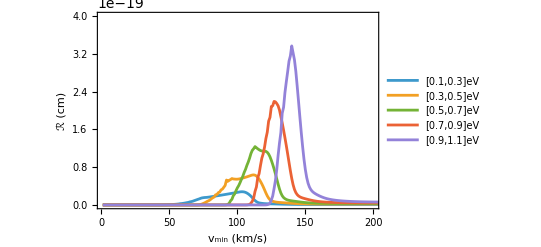

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"curlyRTES/Al_R5_q0M1_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,4 10^-19}},Frame->True,FrameLabel->{{Style["ℛ (cm)", 16], None}, {Style["\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)", 16],Style["TES: m=10 MeV", 16]}},
PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
3.3 10^-19*cm
```

1.66667×10^-14

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_10MeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_10MeV_q=0_5bins.pdf

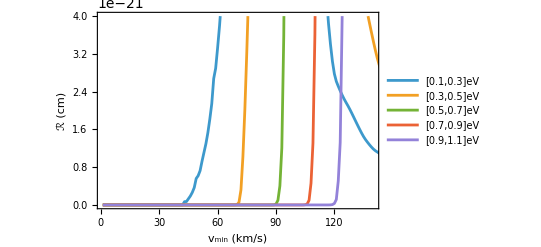

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,140},{0,4 10^-21}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=10 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_10MeV_q=0_5bins_ZOOMED.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_10MeV_q=0_5bins_ZOOMED.pdf

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R10_q0M1.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistAl /cm,PlotRange->{{1, 200}, {0, 2.2 10^-19}}, Frame -> True, FrameLabel->{"v_min (km/s)", "ℛ (cm)"},PlotLegends->{"[0.1, 0.2]eV","[0.2, 0.3]eV","[0.3, 0.4]eV","[0.4, 0.5]eV","[0.5, 0.6]eV","[0.6, 0.7]eV","[0.7, 0.8]eV","[0.8, 0.9]eV","[0.9, 1.0]eV","[1.0, 1.1]eV",LegendLayout->{"Column",2}}]
```

Import::nffil: File /Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R10_q0M1.h5 not found during Import.

ListLinePlot::lpn: 0.0000198 $Failed is not a list of numbers or pairs of numbers.

ListLinePlot[0.0000198 $Failed,PlotRange→{{1,200},{0,2.2×10^-19}},Frame→True,FrameLabel→{v_min (km/s),ℛ (cm)},PlotLegends→{[0.1, 0.2]eV,[0.2, 0.3]eV,[0.3, 0.4]eV,[0.4, 0.5]eV,[0.5, 0.6]eV,[0.6, 0.7]eV,[0.7, 0.8]eV,[0.8, 0.9]eV,[0.9, 1.0]eV,[1.0, 1.1]eV,LegendLayout→{Column,2}}]

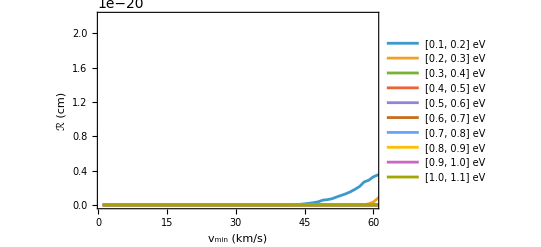

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_10MeV_q=0_SHM_Zoomed.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,60},{0,2.2 10^-20}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=10 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_10MeV_q=0_SHM_Zoomed.pdf",curlyRPlot,"PDF"]
```

```mathematica
vals = RvminAl5[CRlistAl, ηtilde][10 MeV][1,800]
Export[FileNameJoin[Direc,"Events/Al_Events5_SHM_q0M1_Ko.csv"],vals]
```

{4.94967×10^-44,9.8234×10^-44,1.42832×10^-43,1.86592×10^-43,2.25044×10^-43}

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Events/Al_Events5_SHM_q0M1_Ko.csv

```mathematica
Alexp
```

1.84056×10^49

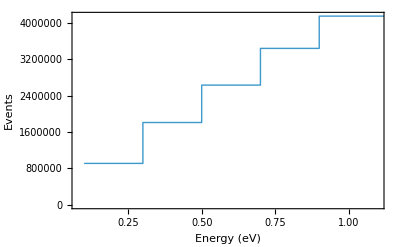

```mathematica
stepData1=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsAl,vals}],1];
ListStepPlot[stepData1,PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

```mathematica
etaList = Table[
ηth[10 MeV][vm kps][238 kps,250 kps, 544 kps]*cm,{vm, 1 , 800 }];
Export[FileNameJoin[Direc,"Eta/EtaHaloM1_Ko.csv"],etaList]
```

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Eta/EtaHaloM1_Ko.csv

```mathematica
etaList = Table[
ηth[1000 MeV][vm kps][238 kps,250 kps, 544 kps]*cm + ηtb[1000 MeV][vm kps][2.16 kps, 11.2 kps] * cm,{vm, 1 , 800 }];
Export[FileNameJoin[Direc,"Eta/EtaBoundM3_Ko.csv"],etaList]
```

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Eta/EtaBoundM3_Ko.csv

```mathematica
etaList = Table[
(0.75ηth[10 MeV][vm kps][238 kps,250 kps, 544 kps]*cm+0.25ηtd[10 MeV][vm kps][70 kps,100 kps, 714 kps] * cm),{vm, 1 , 800 }];
Export[FileNameJoin[Direc,"Eta/EtaDiskM1_Ko_25percent.csv"],etaList]
```

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Eta/EtaDiskM1_Ko_25percent.csv

```mathematica
etaList = Table[
(0.95ηth[10 MeV][vm kps][238 kps,250 kps, 544 kps]*cm+0.05ηtd[10 MeV][vm kps][70 kps,100 kps, 714 kps] * cm),{vm, 1 , 800 }];
Export[FileNameJoin[Direc,"Eta/EtaDiskM1_Ko_5percent.csv"],etaList]
```

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Eta/EtaDiskM1_Ko_5percent.csv

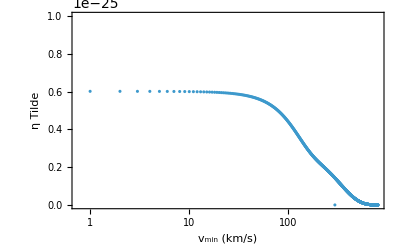

```mathematica
ListPlot[etaList,
PlotStyle->Thick,
Frame->True,
FrameLabel->{"v_min (km/s)","η Tilde"},
PlotRange->{All,{0, 10^-25}}, 
ScalingFunctions->{"Log","Linear"}]
```

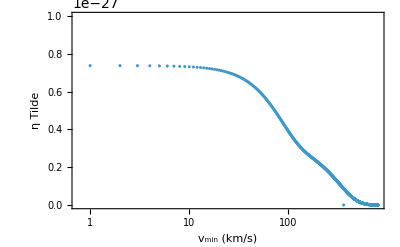

```mathematica
ListPlot[etaList,
PlotStyle->Thick,
Frame->True,
FrameLabel->{"v_min (km/s)","η Tilde"},
PlotRange->{All,{0, 10^-27}}, 
ScalingFunctions->{"Log","Linear"}]
```

```mathematica
Export[FileNameJoin[Direc,"Eta/EtaDiskM3_Ko.csv"],etaList]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Eta/EtaDiskM3_Ko.csv

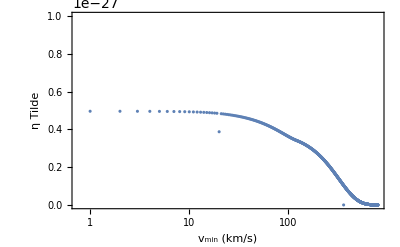

```mathematica
ListPlot[Table[
9/10(ηth[1000 MeV][vm kps][230 kps,240 kps, 600 kps]*cm+1/9 ηtd[1000 MeV][vm kps][230 kps,50 kps, 70 kps] * cm),{vm, 1 , 800 }],
PlotStyle->Thick,
Frame->True,
FrameLabel->{"v_min (km/s)","η Tilde"},
PlotRange->{All,{0, 10^-27}}, 
ScalingFunctions->{"Log","Linear"}]
```

```mathematica
Alexp
```

1.84056×10^49

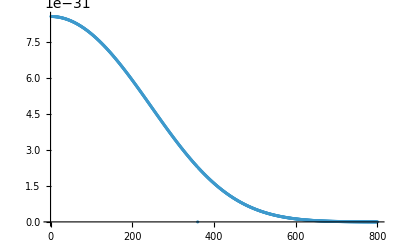

```mathematica
ListPlot[Table[ηth[10 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }]]
```

```mathematica
Export[FileNameJoin[Direc,"etaTilde_M1.h5"],Table[ηth[10 MeV][vm kps][230 kps,240 kps, 600 kps] * cm,{vm, 1 , 800 }]]
Export[FileNameJoin[Direc,"etaTilde_M1.csv"],Table[ηth[10 MeV][vm kps][230 kps,240 kps, 600 kps] * cm,{vm, 1 , 800 }]]
```

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/HALOIND/etaTilde_M1.h5

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/HALOIND/etaTilde_M1.csv

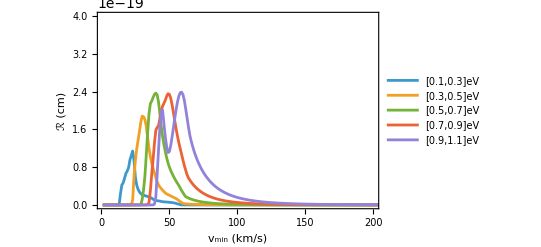

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"curlyRTES/Al_R5_q0M2_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,4 10^-19}},Frame->True,FrameLabel->{{Style["ℛ (cm)", 16], None}, {Style["\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)", 16],Style["TES: m=100 MeV", 16]}},
PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_100MeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_100MeV_q=0_5bins.pdf

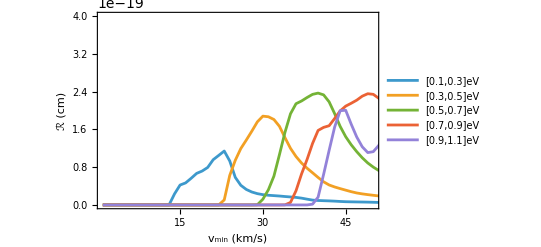

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,50},{0,4 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_100MeV_q=0_5bins_ZOOMED.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_100MeV_q=0_5bins_ZOOMED.pdf

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R10_q0M2.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistAl /cm,PlotRange->{{1, 200}, {0, 2.2 10^-19}}, Frame -> True, FrameLabel->{"v_min (km/s)", "ℛ (cm)"}]
```

Import::nffil: File /Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R10_q0M2.h5 not found during Import.

ListLinePlot::lpn: 0.0000198 $Failed is not a list of numbers or pairs of numbers.

ListLinePlot[0.0000198 $Failed,PlotRange→{{1,200},{0,2.2×10^-19}},Frame→True,FrameLabel→{v_min (km/s),ℛ (cm)}]

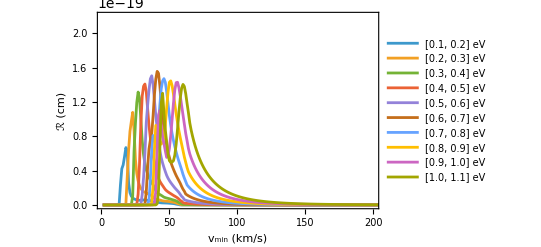

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,2.2 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.73,0.73}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

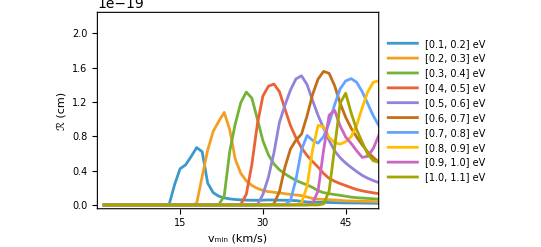

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM_Zoomed.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,50},{0,2.2 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.26,0.75}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM_Zoomed.pdf",curlyRPlot,"PDF"]
```

```mathematica
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM.pdf",%319,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM.pdf

```mathematica
vals = RvminAl5[CRlistAl, ηtilde][100 MeV][1,800]
Export[FileNameJoin[Direc,"Events/Al_Events5_SHM_q0M2_Ko.csv"],vals]
```

{5.67545×10^-45,1.17057×10^-44,1.74225×10^-44,2.29674×10^-44,2.83939×10^-44}

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Events/Al_Events5_SHM_q0M2_Ko.csv

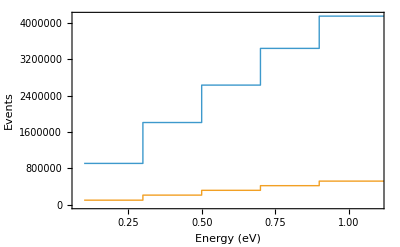

```mathematica
stepData2=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsAl,vals}],1];
ListStepPlot[{stepData1,stepData2},PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

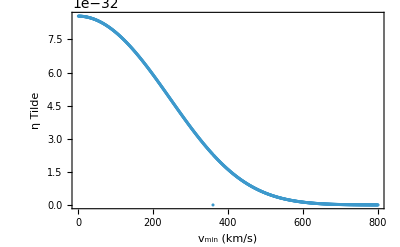

```mathematica
ListPlot[Table[ηth[100 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

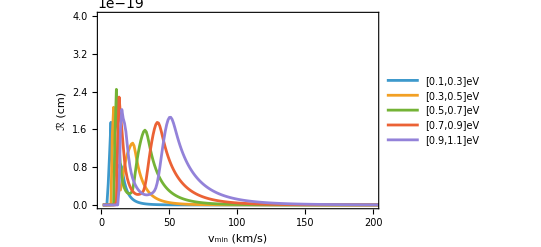

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"curlyRTES/Al_R5_q0M3_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,4 10^-19}},Frame->True,FrameLabel->{{Style["ℛ (cm)", 16], None}, {Style["\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)", 16],Style["TES: m=1 GeV", 16]}},
PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

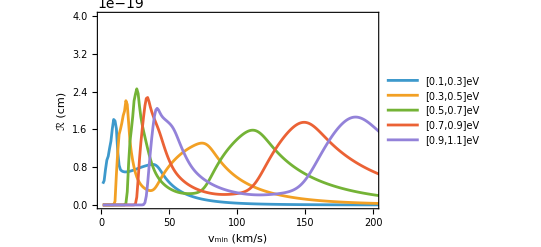

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R5_q0M3_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,4 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_1GeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_1GeV_q=0_5bins.pdf

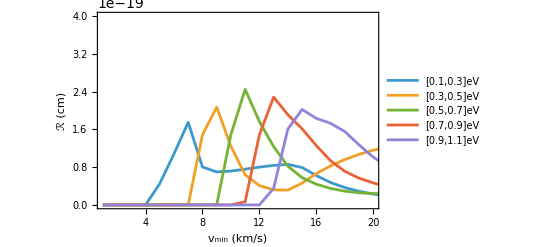

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,20},{0,4 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_1000MeV_q=0_5bins_ZOOMED.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_1000MeV_q=0_5bins_ZOOMED.pdf

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R10_q0M3.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistAl /cm,PlotRange->{{1, 200}, {0, 2.2 10^-19}}, Frame -> True, FrameLabel->{"v_min (km/s)", "ℛ (cm)"}]
```

Import::nffil: File /Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R10_q0M3.h5 not found during Import.

ListLinePlot::lpn: 0.0000198 $Failed is not a list of numbers or pairs of numbers.

ListLinePlot[0.0000198 $Failed,PlotRange→{{1,200},{0,2.2×10^-19}},Frame→True,FrameLabel→{v_min (km/s),ℛ (cm)}]

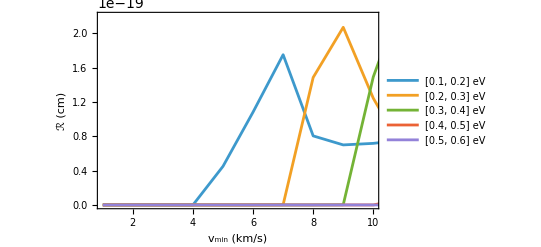

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_1GeV_q=0_SHM_Zoomed.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,10},{0,2.2 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.27,0.75}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_1GeV_q=0_SHM_Zoomed.pdf",curlyRPlot,"PDF"]
```

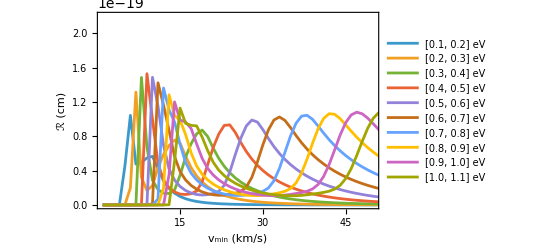

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_1GeV_q=0_SHM.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,50},{0,2.2 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.72,0.75}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_1GeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

```mathematica
ηtilde[5]
```

ηtilde[5]

```mathematica
RvminAl5custom[CRlistAl  * Alexp, ηtilde][100 MeV][200][5, 0.51758]
```

{81561.4,164915.,245018.,328154.,405539.}

```mathematica
vals = RvminAl5custom[CRlistAl, ηtilde][1000 MeV][200][5,108];
```

Part::pkspec1: The expression 2.93207 cannot be used as a part specification.

Part::pkspec1: The expression 4.86414 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
vals = RvminAl5[CRlistAl, ηtilde][1000 MeV][1,800]
Export[FileNameJoin[Direc,"Events/Al_Events5_SHM_q0M3_Ko.csv"],vals]
```

{5.74109×10^-46,1.15497×10^-45,1.74196×10^-45,2.30029×10^-45,2.84975×10^-45}

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Events/Al_Events5_SHM_q0M3_Ko.csv

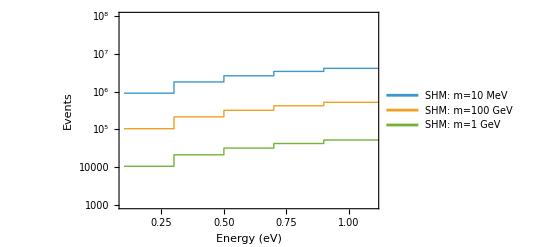

```mathematica
stepData3=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsAl,vals}],1];
EventsSHM = ListStepPlot[{stepData1, stepData2, stepData3},PlotStyle->Thick,Frame->True,
FrameLabel->{{"Events", None}, {"Energy (eV)","TES events for 8200 ng・month"}},
PlotRange->{{0.1,1.1},{10^3,10^8}},
PlotLegends->Placed[LineLegend[{"SHM: m=10 MeV","SHM: m=100 GeV","SHM: m=1 GeV"},LegendLayout->{"Column",1}, LabelStyle->Directive[8]],Scaled[{0.15,0.85}]],
ScalingFunctions->"Log"]
```

```mathematica
kps
```

3.32323×10^-6

```mathematica
Export[FileNameJoin[Direc,"results/Events/Events_TES_SHM_q=0_5bins.pdf"],EventsSHM,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/Events/Events_TES_SHM_q=0_5bins.pdf

```mathematica
ListPlot[Table[ηth[1000 MeV][vm kps][230 kps,240 kps, 600 kps] * cm,{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

```mathematica
(*MKID*)
(* Use imported data *)
```

```mathematica
binsTiN10={{0.2,0.3},{0.3,0.4},{0.4,0.5},{0.5,0.6},{0.6,0.7},{0.7,0.8},{0.8,0.9},{0.9,1.0},{1.0,1.1}};
binsTiN={{0.2,0.3},{0.3,0.5},{0.5,0.7},{0.7,0.9},{0.9,1.1}};
```

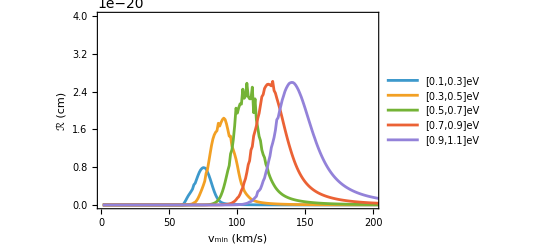

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R5_q0M1_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistTiN/cm,PlotRange->{{1,200},{0,4 10^-20}},Frame->True,FrameLabel->{{Style["ℛ (cm)", 16], None}, {Style["\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)", 16],Style["MKID: m=10 MeV", 16]}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_MKID_10MeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_MKID_10MeV_q=0_5bins.pdf

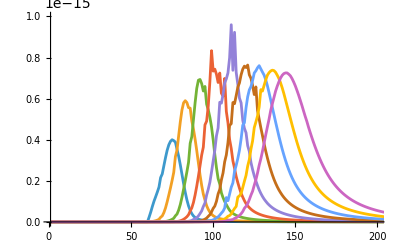

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R10_q0M1.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}}]
```

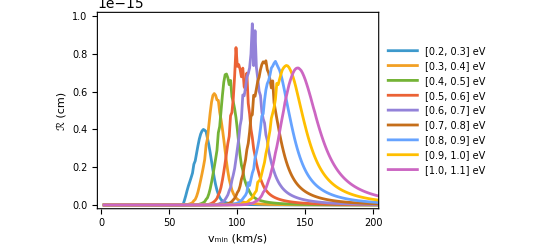

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_10MeV_q=0_SHM.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","MKID: m=10 MeV"}},PlotLegends->Placed[LineLegend[{"[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",1}, LabelStyle->Directive[8]],Scaled[{0.15,0.52}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_10MeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

```mathematica
vals = RvminTiN[CRlistTiN, ηtilde][10 MeV][1,800]
Export[FileNameJoin[Direc,"TiN_Events10_q0M1.csv"],vals]
```

{1.70213×10^-50,2.55884×10^-50,3.22273×10^-50,3.97149×10^-50,4.67044×10^-50,5.15322×10^-50,5.68153×10^-50,6.18928×10^-50,6.61773×10^-50}

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/HALOIND/TiN_Events10_q0M1.csv

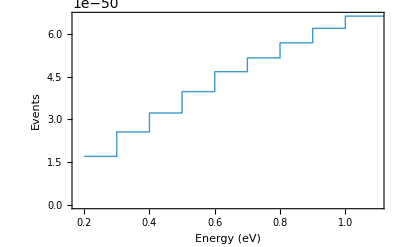

```mathematica
stepData=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsTiN,vals}],1];
ListStepPlot[stepData,PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

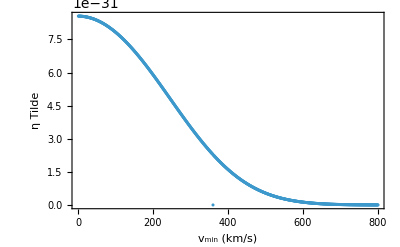

```mathematica
ListPlot[Table[ηth[10 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

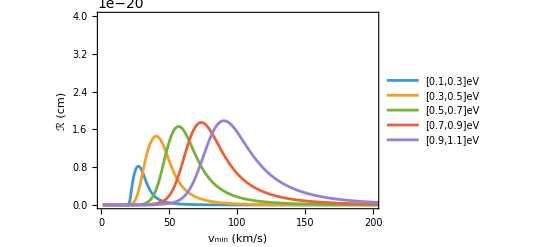

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R5_q0M2_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistTiN/cm,PlotRange->{{1,200},{0,4 10^-20}},Frame->True,FrameLabel->{{Style["ℛ (cm)", 16], None}, {Style["\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)", 16],Style["MKID: m=100 MeV", 16]}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_MKID_100MeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_MKID_100MeV_q=0_5bins.pdf

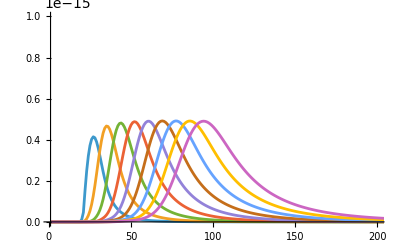

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R10_q0M2.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}}]
```

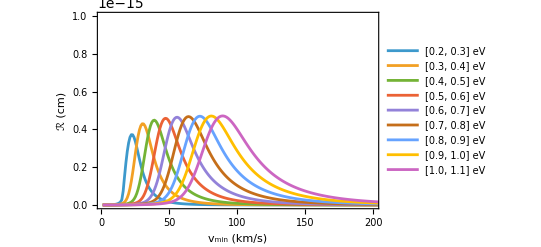

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_100MeV_q=0_SHM.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","MKID: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.73,0.73}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_100MeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

```mathematica
vals = RvminTiN[CRlistTiN, ηtilde][100 MeV][1,800]
Export[FileNameJoin[Direc,"TiN_Events10_q0M2.csv"],vals]
```

{1.64989×10^-51,2.53733×10^-51,3.23167×10^-51,3.90337×10^-51,4.54904×10^-51,5.16518×10^-51,5.74863×10^-51,6.29662×10^-51,6.80691×10^-51}

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/HALOIND/TiN_Events10_q0M2.csv

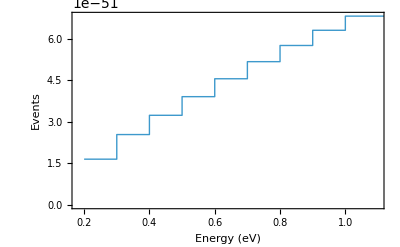

```mathematica
stepData=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsTiN,vals}],1];
ListStepPlot[stepData,PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

```mathematica
ListPlot[Table[ηth[100 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

-Graphics-

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R5_q0M3_Ko_refined.h5"],{"Datasets","Dataset1"}];
```

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R5_q0M3_Ko_refined.h5"],{"Datasets","Dataset1"}];
```

```mathematica
etaList = Table[
ηth[1000 MeV][(5+ (i - 1)0.51758) kps][230 kps,240 kps, 600 kps]*cm + ηtb[1000 MeV][(5 + (i - 1)0.51758) kps][2.441876042996079 kps, 11.2 kps] * cm,{i, 1, 200 }];
```

```mathematica
CRlistAl.etaList * Alexp
```

{1.32726×10^18,8.18033×10^15,1.69766×10^13,2.66828×10^9,3.24616×10^9}

```mathematica
Export[FileNameJoin[Direc,"Al_Events5_q0M3_exposure.csv"],CRlistAl.etaList * Alexp]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_Events5_q0M3_exposure.csv

```mathematica
etaList = Table[
ηth[1000 MeV][(6 + (i - 1)0.51256) kps][230 kps,240 kps, 600 kps]*cm + ηtb[1000 MeV][(6 + (i - 1)0.51256) kps][2.441876042996079 kps, 11.2 kps] * cm,{i, 1, 200 }];
```

```mathematica
CRlistTiN.etaList * TiNexp
```

{8.07251×10^13,9.34623×10^12,4.6719×10^10,3.95002×10^9,3.38977×10^9}

```mathematica
Export[FileNameJoin[Direc,"TiN_Events5_q0M3_exposure.csv"],CRlistTiN.etaList * TiNexp]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/TiN_Events5_q0M3_exposure.csv

```mathematica
RvminTiN5custom[CRlistTiN, ηtilde][1000 MeV][200][6, 0.51256]
```

{8.63544×10^-47,2.89575×10^-46,4.19181×10^-46,5.04992×10^-46,5.0265×10^-46}

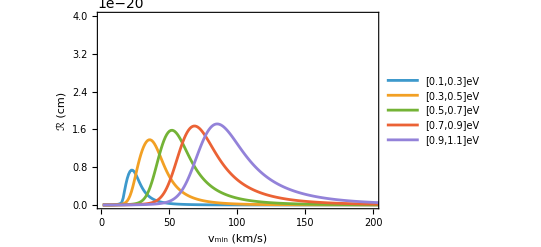

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R5_q0M3_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistTiN/cm,PlotRange->{{1,200},{0,4 10^-20}},Frame->True,FrameLabel->{{Style["ℛ (cm)", 16], None}, {Style["\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)", 16],Style["MKID: m=1 GeV", 16]}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_MKID_1GeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_MKID_1GeV_q=0_5bins.pdf

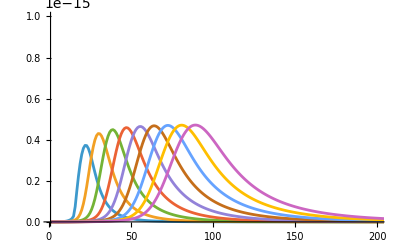

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R10_q0M3.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}}]
```

```mathematica
curlyRPlot = ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","MKID: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.73,0.73}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_1GeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

-Graphics-

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_1GeV_q=0_SHM.pdf

```mathematica
vals = RvminTiN[CRlistTiN, ηtilde][1000 MeV][1,800]
Export[FileNameJoin[Direc,"TiN_Events10_q0M3.csv"],vals]
```

```mathematica
stepData=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsTiN,vals}],1];
ListStepPlot[stepData,PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

```mathematica
ListPlot[Table[ηth[1000 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```